## initial

```mathematica
Clear[kf0,B,ifun0];

kf0[μ_,vf_,cq_,B_,θ_,chi_]:=Block[{e=1},

1/6^(2/3)(-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(27 B^2 cq e^2 vf^3 Cos[θ]^2-4 μ^3))^(1/3) (2^(1/3)/(cq vf)+(2 3^(1/3) μ)/((-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(27 B^2 cq e^2 vf^3 Cos[θ]^2-4 μ^3))^(2/3)))
];


ifun0[μ_,vf_,cq_,B_,chi_]:=Block[{e=1,θ,kfvals,dat,len,kf,list},
kfvals[θ_]=1/6^(2/3)(-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(1/3) (2^(1/3)/(cq vf)+(2 3^(1/3) μ)/((-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(2/3)));
dat=Table[{θ,kfvals[θ]//Chop},{θ,0,π,π/20}];
len=Length[dat];
list=Table[{dat[[i,1]]+dat[[len,1]]+π/20,dat[[len-i,2]] },{i,1,len-1}];
dat=Join[dat,list];
Interpolation[dat,PeriodicInterpolation->True]
];
```

```mathematica
Solve[cq vf kf^2==μ, kf]
```

{{kf→-(√μ)/(√cq √vf)},{kf→(√μ)/(√cq √vf)}}

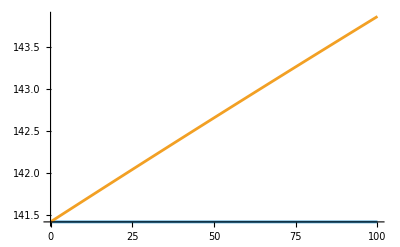

```mathematica
rep={μ->0.1,cq->0.001,vf->0.005,θ->π,chi->1,e->1}(* nonzero contr regime for linear band *);Plot[{(√μ)/(√cq √vf)/.rep,kf0[μ,vf,cq,B,θ,chi]/.rep},{B,0,100}]
```

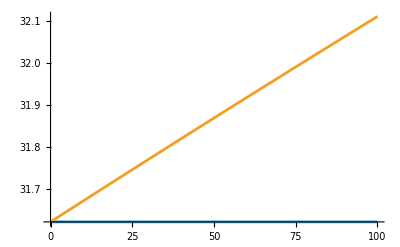

```mathematica
rep={μ->0.5,cq->0.1,vf->0.005,θ->π,chi->1,e->1}(* nonzero contr regime for flat band *);Plot[{(√μ)/(√cq √vf)/.rep,kf0[μ,vf,cq,B,θ,chi]/.rep},{B,0,100}]
```

## matrix

```mathematica
Clear[G];G=(*2 flat bands*)(ct2 ctp2+1/2 st2 stp2);
```

```mathematica
Clear[eq,Λ11byτ,Λ21byτ,Λ10byτ,Λ20byτ,lhs1,lhs2,lhs3,lhs4,rhs1,rhs2,rhs3,rhs4,λ,a,b,h11,h21,h10,c11,eqn1,eqn2,eqn3,eqn4,eqn5,eqn6,eqn7,eqn8,eqn9,eqn10,eqn11];
Λ10byτ=(-h10+c10 st2(* Sin[θ]^2*)+d10 ct2(* Cos[θ]^2*));
Λ20byτ=(-h10+c20 st2+d20 ct2);

(* -Graphics- ; -Graphics-*)
lhs3=c10 st2+d10 ct2;       lhs4=c20 st2+d20 ct2;

rhs3=tra00 intθpf10 G(-h10+c10 stp2+d10 ctp2)+ter00 intθpf20 G(-h20+c20 stp2+d20 ctp2)//FullSimplify;

rhs4=tra00 intθpf20 G(-h20+c20 stp2+d20 ctp2)+ter00 intθpf10 G(-h10+c10 stp2+d10 ctp2)//FullSimplify;


eq=lhs3-rhs3;
eqn10=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1},{ct2,0,0}]//FullSimplify;
eqn11=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0},{ct2,0,1}]//FullSimplify;
eq== eqn10 st2+ eqn11 ct2//FullSimplify

eq=lhs4-rhs4;
eqn13=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1},{ct2,0,0}]//FullSimplify;
eqn14=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0},{ct2,0,1}]//FullSimplify;
eq== eqn13 st2+ eqn14 ct2//FullSimplify

(* Print["charge consvn:"];*)
intθf10 Λ10byτ +intθf20 Λ20byτ
```

True

True

intθf10 (ct2 d10-h10+c10 st2)+intθf20 (ct2 d20-h10+c20 st2)

```mathematica
Clear[arr,array,array1,cmat];arr=CoefficientArrays[{ eqn10==0,eqn11==0,eqn13==0,eqn14==0},{c10,d10,c20,d20}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
rep={intθpf11->af11,intθpf21->af21,intθpf10->af10,intθpf20->af20,ctp4->ct4,stp4->st4,stp2->st2,ctp2->ct2};
cmat=Expand[cmat/.rep];
array[[1]]=Expand[array[[1]]/.rep];
rep1={af10 ct2^3->ct2ct2ct210,af20 ct2^3->ct2ct2ct220,af10 ct2^2 st2->ct2ct2at210,af20 ct2^2 st2->ct2ct2at220,af10 ct2 st2->ct2st210,af10 ct2^2->ct2ct210,af20 ct2 st2->ct2st220,af20 ct2^2->ct2ct220,af20 st2^2->st2st220,af10 st2^2->st2st210,af20 h20 st2->hst220,af10 h10 st2->hst210,af10 ct2 h10->hct210,af20 ct2 h20->hct220,
(***********)af20 ct2->ct220,af10 ct2->ct210, af10->zero10,af20->zero20,(**************************)af21 h21 st2->hst221,af21 h21 st4->hst421,af11 ct4 h11->hct411,af21 ct4 h21->hct421,af11 h11 st4->hst411,af11 h11 st2->hst211,af10 h10->hzero10,af20 h20->hzero20,(**************)af11 ct4 st4->ct4st411,af11 ct4 st2->ct4st211,af11 ct4->ct411,af11 st4 st2->st4st211, af11 st4->st411,af11 st2->st211,af11 (ct4-st2+st4)->ct411-st211+st411,af11 ct4^2->ct4ct411,af11 st4^2->st4st411,af11 st2^2->st2st211,(**********)af21 ct4 st4->ct4st421,af21 ct4 st2->ct4st221,af21 ct4->ct421,af21 st4 st2->st4st221, af21 st4->st421,af21 st2->st221,af21 (ct4-st2+st4)->ct421-st221+st421,af21 ct4^2->ct4ct421,af21 st4^2->st4st421,af21 st2^2->st2st221,(********)af10 st2->st210,af10 st2^2->st2st210,af20 st2 ->st220,af20 st2^2->st2st220,af10->zero10,af20->zero20};
MatrixForm[cmat/.rep1]//FullSimplify
MatrixForm[array[[1]]/.rep1]//FullSimplify
MatrixRank[cmat]
```

(1-(st2st210 tra00)/2 | -(ct2st210 tra00)/2 | -(st2st220 ter00)/2 | -(ct2st220 ter00)/2
-ct2st210 tra00 | 1-ct2ct210 tra00 | -ct2st220 ter00 | -ct2ct220 ter00
-(st2st210 ter00)/2 | -(ct2st210 ter00)/2 | 1-(st2st220 tra00)/2 | -(ct2st220 tra00)/2
-ct2st210 ter00 | -ct2ct210 ter00 | -ct2st220 tra00 | 1-ct2ct220 tra00)

(1/2 (hst220 ter00+hst210 tra00)
hct220 ter00+hct210 tra00
1/2 (hst210 ter00+hst220 tra00)
hct210 ter00+hct220 tra00)

4

```mathematica
(*-ct210 h10 ter00-ct220 h20 tra00 *)
```

## sigma

```mathematica
Clear[sig,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];

sig[B_,μ_,vf_,cq_,tra00_,ter00_]:=Block[{e=1,vvec10,vvec20,θ,ϕ=0,θp,chi,vomm10,vomm20,vdotk10,vdotk20,colvec,mat,sol,Λ10,Λ20,λ10,c10,λ20,c20,matr,kf10,kf20,h10,h20,τ10,τ20,f10,f20,zero10,st210,st2st210,zero20,st220,ct220,ct2st210,ct2st220,ct210,st2st220,hzero10,hzero20,hst210,hct210,hst220,hct220,ct2ct210,ct2ct220,d10,d20,conteq0,int10,int20,s10,s20},

chi=1;
(******** first node ***************)

(***** flat band *****)

kf10[θ_]=ifun0[μ,vf,cq,B,chi][θ];

vvec10[θ_]=2cq kf10[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm10[θ_]=(-  e B vf)/(kf10[θ])^2{Cos[ϕ] Sin[2 θ], Sin[2 θ] Sin[ϕ], Cos[2 θ]};
(* -Graphics-;-Graphics- *)
h10[θ_]=2 cq kf10[θ] vf Cos[θ]-(B   e vf Cos[2 θ])/kf10[θ]^2;
vdotk10[θ_]=(vf (2cq kf10[θ]^3-B   e Cos[θ]))/kf10[θ];
(**************************************************)
(******** second node ***************)
chi=-1;

(***** flat band *****)

kf20[θ_]=ifun0[μ,vf,cq,B,chi][θ];
vvec20[θ_]=2cq kf20[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm20[θ_]=(e B vf)/kf20[θ]^2{Cos[ϕ] Sin[2 θ], Sin[2 θ] Sin[ϕ], Cos[2 θ]};
h20[θ_]=2 cq kf20[θ] vf Cos[θ]+(B e vf Cos[2 θ])/kf20[θ]^2;
vdotk20[θ_]=(vf (2cq kf20[θ]^3+B e Cos[θ]))/kf20[θ];
(***************************************************************************************************************)
(* -Graphics- *)
(********* ter00 (cos[θ]^2 cos[θp]^2+1/2 sin[θ]^2 sin[θp]^2) ************)
τ10[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(***conj. node **************************************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}](* using (ct2 ctp2+1/2 st2 stp2) *))^-1//Quiet;
(********************************)
τ20[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using (ct2 ctp2+1/2 st2 stp2) *))^-1//Quiet;
(********************************)

(*-Graphics-*)
f10[θ_]=(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]] τ10[θ];
f20[θ_]=(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]] τ20[θ];


(*zero10=Quiet[NIntegrate [f10[θ],{θ,0,π}]];*)
st210=Quiet[NIntegrate [f10[θ] Sin[θ]^2,{θ,0,π}]];
ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^2,{θ,0,π}]];
st2st210=Quiet[NIntegrate [f10[θ] Sin[θ]^4,{θ,0,π}]];
ct2st210=Quiet[NIntegrate [f10[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^4,{θ,0,π}]];

(*zero20=Quiet[NIntegrate [f20[θ],{θ,0,π}]];*)
st220=Quiet[NIntegrate [f20[θ] Sin[θ]^2,{θ,0,π}]];
ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^2,{θ,0,π}]];
st2st220=Quiet[NIntegrate [f20[θ] Sin[θ]^4,{θ,0,π}]];
ct2st220=Quiet[NIntegrate [f20[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^4,{θ,0,π}]];

hzero10=Quiet[NIntegrate [f10[θ]h10[θ],{θ,0,π}]];
hst210=Quiet[NIntegrate [f10[θ]h10[θ] Sin[θ]^2,{θ,0,π}]];
hct210=Quiet[NIntegrate [f10[θ]h10[θ] Cos[θ]^2,{θ,0,π}]];

hzero20=Quiet[NIntegrate [f20[θ]h20[θ],{θ,0,π}]];
hst220=Quiet[NIntegrate [f20[θ]h20[θ] Sin[θ]^2,{θ,0,π}]];
hct220=Quiet[NIntegrate [f20[θ]h20[θ] Cos[θ]^2,{θ,0,π}]];


colvec=({{1/2 (hst220 ter00+hst210 tra00)}, {hct220 ter00+hct210 tra00}, {1/2 (hst210 ter00+hst220 tra00)}, {hct210 ter00+hct220 tra00}});
matr=({{1-(st2st210 tra00)/2, -(ct2st210 tra00)/2, -(st2st220 ter00)/2, -(ct2st220 ter00)/2}, {-ct2st210 tra00, 1-ct2ct210 tra00, -ct2st220 ter00, -ct2ct220 ter00}, {-(st2st210 ter00)/2, -(ct2st210 ter00)/2, 1-(st2st220 tra00)/2, -(ct2st220 tra00)/2}, {-ct2st210 ter00, -ct2ct210 ter00, -ct2st220 tra00, 1-ct2ct220 tra00}});
mat=matr.{c10,d10,c20,d20};
conteq0=(-hzero10 +c10 st210+d10 ct210)+(-hzero20 +c20 st220+d20 ct220);


sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,conteq0==0},{c10,d10,c20,d20}],1];

Λ10[θ_]=τ10[θ](-h10[θ]+c10 Sin[θ]^2+d10 Cos[θ]^2)/.sol;
Λ20[θ_]=τ20[θ](-h10[θ]+c20 Sin[θ]^2+d20 Cos[θ]^2)/.sol;
(* -Graphics-*)

int10[θ_]=-(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]]e(vvec10[θ]+vomm10[θ])[[3]] Λ10[θ];int20[θ_]=-(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]]e(vvec20[θ]+vomm20[θ])[[3]] Λ20[θ];

s10=Chop[NIntegrate[int10[θ],{θ,0,π}]]//Quiet;
s20=Chop[NIntegrate[int20[θ],{θ,0,π}]]//Quiet;
(*Print[h10[1],h20[1]];
Print[h10[π-1],h20[π-1]];*)
{B,{s10,s20},s10+s20,MatrixRank[matr],MatrixForm[{c10,d10,c20,d20}/.sol]}
];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;intra=5;inter=2;
sig[0.1,mu,vfval,cqval,intra,inter]
sig[1,mu,vfval,cqval,intra,inter]
```

{0.1,{0.0000285714,0.0000285714},0.0000571429,3,(-5.1725×10^-7
1.03446×10^-6
5.1725×10^-7
-1.03446×10^-6)}

{1,{0.0000285715,0.000028571},0.0000571425,3,(-5.17251×10^-6
0.0000103447
5.17251×10^-6
-0.0000103447)}

```mathematica
sig[10,mu,vfval,cqval,intra,inter]
```

{10,{0.0000285762,0.0000285333},0.0000571095,3,(-0.0000517394
0.000103456
0.0000517394
-0.000103456)}

```mathematica
(-h[θ]+c Sin[θ]^2+d Cos[θ]^2)/.{c->-0.00005173942233749059,d->0.00010345587090479756}
(-h[θ]+c Sin[θ]^2+d Cos[θ]^2)/.{c->0.00005173942233749059,d->-0.00010345587090479756}
```

0.000103456 Cos[θ]^2-h[θ]-0.0000517394 Sin[θ]^2

-0.000103456 Cos[θ]^2-h[θ]+0.0000517394 Sin[θ]^2

```mathematica
NIntegrate[0.00010345587090479756 Cos[θ]^2-0.00005173942233749059 Sin[θ]^2-θ,{θ,0,π}]
NIntegrate[-0.00010345587090479756 Cos[θ]^2+0.00005173942233749059 Sin[θ]^2-θ,{θ,0,π}]
```

-4.93472

-4.93488

## sigma at B=0

```mathematica
Clear[sig0,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];

sig0[μ_,vf_,cq_,tra00_,ter00_]:=Block[{e=1,vvec10,vvec20,θ,ϕ=0,θp,chi,vomm10,vomm20,vdotk10,vdotk20,colvec,mat,sol,Λ10,Λ20,λ10,c10,λ20,c20,matr,kf10,kf20,h10,h20,τ10,τ20,f10,f20,zero10,st210,st2st210,zero20,st220,ct220,ct2st210,ct2st220,ct210,st2st220,hzero10,hzero20,hst210,hct210,hst220,hct220,ct2ct210,ct2ct220,d10,d20,conteq0,int10,int20,s10,s20},

chi=1;
(******** first node ***************)

(***** flat band *****)

kf10[θ_]=(√μ)/(√cq √vf);

vvec10[θ_]=2vf cq kf10[θ]{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm10[θ_]={0,0,0};
h10[θ_]=2 cq kf10[θ] vf Cos[θ];
vdotk10[θ_]=2vf cq kf10[θ]^2;
(**************************************************)
(******** second node ***************)
chi=-1;

(***** flat band *****)

kf20[θ_]=(√μ)/(√cq √vf);
vvec20[θ_]=2cq kf20[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm20[θ_]={0,0,0};
h20[θ_]=2 cq kf20[θ] vf Cos[θ];
vdotk20[θ_]=2vf cq (kf20[θ])^2;
(***************************************************************************************************************)
(* -Graphics- *)
(********************************)
τ10[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(***conj. node **************************************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}](* using (ct2 ctp2+1/2 st2 stp2) *))^-1//Quiet;
(********************************)
τ20[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using (ct2 ctp2+1/2 st2 stp2) *))^-1//Quiet;
(********************************)

(*-Graphics-*)
f10[θ_]=(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]] τ10[θ];
f20[θ_]=(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]] τ20[θ];


st210=Quiet[NIntegrate [f10[θ] Sin[θ]^2,{θ,0,π}]];
ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^2,{θ,0,π}]];
st2st210=Quiet[NIntegrate [f10[θ] Sin[θ]^4,{θ,0,π}]];
ct2st210=Quiet[NIntegrate [f10[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^4,{θ,0,π}]];

st220=Quiet[NIntegrate [f20[θ] Sin[θ]^2,{θ,0,π}]];
ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^2,{θ,0,π}]];
st2st220=Quiet[NIntegrate [f20[θ] Sin[θ]^4,{θ,0,π}]];
ct2st220=Quiet[NIntegrate [f20[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^4,{θ,0,π}]];

hzero10=Quiet[NIntegrate [f10[θ]h10[θ],{θ,0,π}]];
hst210=Quiet[NIntegrate [f10[θ]h10[θ] Sin[θ]^2,{θ,0,π}]];
hct210=Quiet[NIntegrate [f10[θ]h10[θ] Cos[θ]^2,{θ,0,π}]];

hzero20=Quiet[NIntegrate [f20[θ]h20[θ],{θ,0,π}]];
hst220=Quiet[NIntegrate [f20[θ]h20[θ] Sin[θ]^2,{θ,0,π}]];
hct220=Quiet[NIntegrate [f20[θ]h20[θ] Cos[θ]^2,{θ,0,π}]];


colvec=({{1/2 (hst220 ter00+hst210 tra00)}, {hct220 ter00+hct210 tra00}, {1/2 (hst210 ter00+hst220 tra00)}, {hct210 ter00+hct220 tra00}});
matr=({{1-(st2st210 tra00)/2, -(ct2st210 tra00)/2, -(st2st220 ter00)/2, -(ct2st220 ter00)/2}, {-ct2st210 tra00, 1-ct2ct210 tra00, -ct2st220 ter00, -ct2ct220 ter00}, {-(st2st210 ter00)/2, -(ct2st210 ter00)/2, 1-(st2st220 tra00)/2, -(ct2st220 tra00)/2}, {-ct2st210 ter00, -ct2ct210 ter00, -ct2st220 tra00, 1-ct2ct220 tra00}});
mat=matr.{c10,d10,c20,d20};
conteq0=(-hzero10 +c10 st210+d10 ct210)+(-hzero20 +c20 st220+d20 ct220);


sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,conteq0==0},{c10,d10,c20,d20}],1];

Λ10[θ_]=τ10[θ](-h10[θ]+c10 Sin[θ]^2+d10 Cos[θ]^2)/.sol;
Λ20[θ_]=τ20[θ](-h10[θ]+c20 Sin[θ]^2+d20 Cos[θ]^2)/.sol;

int10[θ_]=-(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]]e(vvec10[θ]+vomm10[θ])[[3]] Λ10[θ];int20[θ_]=-(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]]e(vvec20[θ]+vomm20[θ])[[3]] Λ20[θ];

s10=Chop[NIntegrate[int10[θ],{θ,0,π}]]//Quiet;
s20=Chop[NIntegrate[int20[θ],{θ,0,π}]]//Quiet;

{s10,s20,s10+s20,MatrixRank[matr],MatrixForm[{c10,d10,c20,d20}/.sol]}
];
```

```mathematica
sig0[mu,vfval,cqval,5,2]
```

{0.0000285714,0.0000285714,0.0000571429,3,(-1.21113×10^-18
8.23971×10^-19
-2.45974×10^-19
1.0467×10^-18)}

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat0=0.001;
val1=5;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000266667,0.0000266667,0.0000533333,3,(1.17542×10^-18
-1.78203×10^-19
3.66179×10^-19
-3.13076×10^-19)}

{{0.1,0.0000266667},{1.1,0.0000266667},{2.1,0.0000266668},{3.1,0.000026667},{4.1,0.0000266672},{5.1,0.0000266676},{6.1,0.0000266679},{7.1,0.0000266684},{8.1,0.0000266689},{9.1,0.0000266695},{10.1,0.0000266701},{15,0.0000266742},{20,0.0000266798},{25,0.0000266867},{30,0.0000266946},{35,0.0000267033},{40,0.0000267123},{45,0.000026721},{50,0.0000267287},{55,0.0000267346},{60,0.0000267374}}

{{0.1,0.0000266667},{1.1,0.0000266662},{2.1,0.0000266651},{3.1,0.0000266631},{4.1,0.0000266605},{5.1,0.0000266571},{6.1,0.000026653},{7.1,0.0000266482},{8.1,0.0000266426},{9.1,0.0000266363},{10.1,0.0000266293},{15,0.000026584},{20,0.0000265192},{25,0.0000264352},{30,0.0000263315},{35,0.0000262074},{40,0.0000260621},{45,0.0000258946},{50,0.0000257034},{55,0.0000254869},{60,0.0000252432}}

{{0.1,0.0000533333},{1.1,0.0000533329},{2.1,0.0000533319},{3.1,0.0000533301},{4.1,0.0000533278},{5.1,0.0000533247},{6.1,0.000053321},{7.1,0.0000533166},{8.1,0.0000533115},{9.1,0.0000533058},{10.1,0.0000532994},{15,0.0000532582},{20,0.000053199},{25,0.0000531219},{30,0.0000530261},{35,0.0000529107},{40,0.0000527744},{45,0.0000526155},{50,0.0000524321},{55,0.0000522215},{60,0.0000519806}}

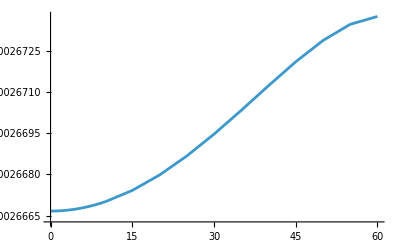

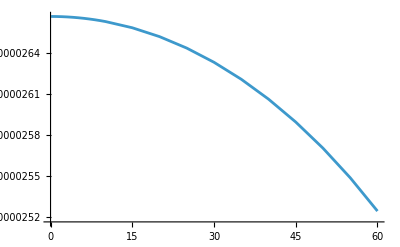

```mathematica
ListLinePlot[list1]
ListLinePlot[list2]
```

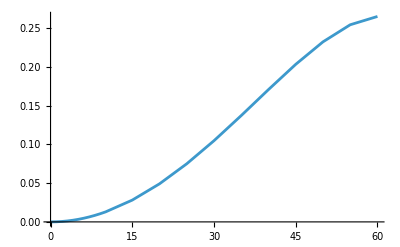

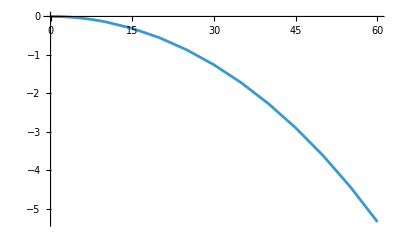

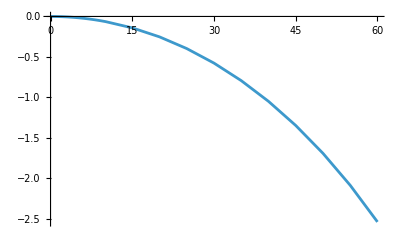

```mathematica
len=Length[list1];
x=0.0000533333333333333;
rat1=0.5;
scale=1/x;
dat1=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]];
ListLinePlot[%]
dat2=Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]];
ListLinePlot[%]
dat3=Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]];
ListLinePlot[%]
```

## Results

### set 1

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1=5;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000266667,0.0000266667,0.0000533333,3,(1.17542×10^-18
-1.78203×10^-19
3.66179×10^-19
-3.13076×10^-19)}

```mathematica
list1={{-10.1,0.00002667011248985518},{-9.1,0.000026669469055778537},{-8.1,0.000026668890619375042},{-7.1,0.000026668377853437767},{-6.1,0.000026667931349814518},{-5.1,0.00002666755162042305},{-4.1,0.000026667239098125966},{-3.0999999999999996,0.000026666994137468125},{-2.0999999999999996,0.0000266668170152791},{-1.0999999999999996,0.000026666707931142457},{-0.09999999999999964,0.000026666667007733705},{-60,0.000026737444288334162},{-55,0.00002673458417887193},{-50,0.000026728695707592063},{-45,0.00002672095231411117},{-40,0.00002671225486813508},{-35,0.000026703302162132028},{-30,0.000026694639216892758},{-25,0.0000266866910945567},{-20,0.000026679786914966186},{-15,0.000026674177028358456},{0.1,0.00002666666700773371},{1.1,0.00002666670793114246},{2.1,0.000026666817015279095},{3.1,0.000026666994137468125},{4.1,0.000026667239098125963},{5.1,0.000026667551620423053},{6.1,0.000026667931349814515},{7.1,0.000026668377853437767},{8.1,0.000026668890619375042},{9.1,0.000026669469055778534},{10.1,0.000026670112489855176},{15,0.00002667417702835846},{20,0.00002667978691496619},{25,0.0000266866910945567},{30,0.000026694639216892764},{35,0.00002670330216213203},{40,0.00002671225486813508},{45,0.00002672095231411117},{50,0.000026728695707592066},{55,0.00002673458417887193},{60,0.000026737444288334162}};
list2={{-10.1,0.000026629269374419535},{-9.1,0.00002663631934994006},{-8.1,0.000026642630540964697},{-7.1,0.0000266482044091576},{-6.1,0.000026653042242053175},{-5.1,0.000026657145154613575},{-4.1,0.000026660514090572337},{-3.0999999999999996,0.000026663149823567993},{-2.0999999999999996,0.000026665052958070796},{-1.0999999999999996,0.000026666223930105285},{-0.09999999999999964,0.00002666666300777056},{-60,0.000025243199867154455},{-55,0.0000254869434472329},{-50,0.000025703380314879247},{-45,0.00002589456803747435},{-40,0.00002606214819126683},{-35,0.000026207439451900967},{-30,0.000026331503170939514},{-25,0.00002643519046100052},{-20,0.00002651917642013563},{-15,0.000026583985110872897},{0.1,0.00002666666300777056},{1.1,0.000026666223930105285},{2.1,0.000026665052958070793},{3.1,0.00002666314982356799},{4.1,0.00002666051409057234},{5.1,0.000026657145154613575},{6.1,0.000026653042242053175},{7.1,0.000026648204409157592},{8.1,0.000026642630540964697},{9.1,0.00002663631934994006},{10.1,0.000026629269374419538},{15,0.000026583985110872897},{20,0.00002651917642013563},{25,0.000026435190461000524},{30,0.00002633150317093951},{35,0.000026207439451900967},{40,0.00002606214819126683},{45,0.000025894568037474347},{50,0.000025703380314879247},{55,0.000025486943447232907},{60,0.000025243199867154455}};
list3={{-10.1,0.00005329938186427472},{-9.1,0.0000533057884057186},{-8.1,0.00005331152116033974},{-7.1,0.000053316582262595367},{-6.1,0.00005332097359186769},{-5.1,0.00005332469677503663},{-4.1,0.0000533277531886983},{-3.0999999999999996,0.00005333014396103612},{-2.0999999999999996,0.00005333186997334989},{-1.0999999999999996,0.00005333293186124774},{-0.09999999999999964,0.00005333333001550426},{-60,0.00005198064415548862},{-55,0.000052221527626104835},{-50,0.000052432076022471306},{-45,0.00005261552035158552},{-40,0.000052774403059401915},{-35,0.000052910741614032995},{-30,0.00005302614238783227},{-25,0.00005312188155555722},{-20,0.000053198963335101815},{-15,0.00005325816213923135},{0.1,0.00005333333001550427},{1.1,0.00005333293186124775},{2.1,0.00005333186997334989},{3.1,0.00005333014396103612},{4.1,0.0000533277531886983},{5.1,0.00005332469677503663},{6.1,0.000053320973591867687},{7.1,0.00005331658226259536},{8.1,0.00005331152116033974},{9.1,0.00005330578840571859},{10.1,0.00005329938186427472},{15,0.00005325816213923136},{20,0.00005319896333510182},{25,0.000053121881555557226},{30,0.000053026142387832275},{35,0.000052910741614032995},{40,0.000052774403059401915},{45,0.00005261552035158552},{50,0.00005243207602247131},{55,0.000052221527626104835},{60,0.00005198064415548862}};

len=Length[list1];
x=0.00005333333333333329;
rat1=0.5;
scale=1/x;
dat11=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
dat12=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
dat13=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat2=1;
val1=5;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.00002,0.00002,0.00004,3,(1.44843×10^-18
6.09864×10^-19
9.57147×10^-19
6.09864×10^-19)}

```mathematica
rat2=1;list1={{-10.1,0.00002000022961551768},{-9.1,0.000020000190351309766},{-8.1,0.000020000153614867295},{-7.1,0.000020000119924665713},{-6.1,0.000020000089736880512},{-5.1,0.000020000063446139986},{-4.1,0.000020000041386173905},{-3.0999999999999996,0.000020000023830360413},{-2.0999999999999996,0.000020000010992172716},{-1.0999999999999996,0.00002000000302552718},{-0.09999999999999964,0.000020000000025033908},{-60,0.000019969232844818},{-55,0.000019980568546306553},{-50,0.000019988437016870455},{-45,0.000019993721398533395},{-40,0.000019997102183669802},{-35,0.00001999910910005148},{-30,0.0000200001567035914},{-25,0.00002000056932006503},{-20,0.000020000598779796205},{-15,0.000020000437111926395},{0.1,0.00002000000002503391},{1.1,0.000020000003025527184},{2.1,0.000020000010992172713},{3.1,0.00002000002383036041},{4.1,0.00002000004138617391},{5.1,0.000020000063446139986},{6.1,0.000020000089736880512},{7.1,0.000020000119924665713},{8.1,0.000020000153614867295},{9.1,0.00002000019035130977},{10.1,0.00002000022961551768},{15,0.000020000437111926395},{20,0.0000200005987797962},{25,0.000020000569320065034},{30,0.0000200001567035914},{35,0.00001999910910005148},{40,0.0000199971021836698},{45,0.000019993721398533398},{50,0.000019988437016870455},{55,0.00001998056854630655},{60,0.000019969232844817996}};
list2={{-10.1,0.000019969597278940944},{-9.1,0.000019975328071930914},{-8.1,0.000019980458556059537},{-7.1,0.00001998498984145558},{-6.1,0.000019988922906059507},{-5.1,0.00001999225859678288},{-4.1,0.000019994997630508686},{-3.0999999999999996,0.000019997140594935307},{-2.0999999999999996,0.00001999868794926649},{-1.0999999999999996,0.000019999640024749297},{-0.09999999999999964,0.00001999999702506155},{-60,0.00001884854952893322},{-55,0.00001904483799757728},{-50,0.00001921945047233584},{-45,0.000019373933191055777},{-40,0.00001950952217601861},{-35,0.00001962721206737818},{-30,0.000019727804669126462},{-25,0.000019811943844897906},{-20,0.000019880140908673286},{-15,0.000019932793173812225},{0.1,0.000019999997025061554},{1.1,0.0000199996400247493},{2.1,0.00001999868794926649},{3.1,0.000019997140594935307},{4.1,0.00001999499763050869},{5.1,0.000019992258596782877},{6.1,0.000019988922906059503},{7.1,0.00001998498984145558},{8.1,0.000019980458556059537},{9.1,0.00001997532807193091},{10.1,0.000019969597278940944},{15,0.000019932793173812222},{20,0.000019880140908673286},{25,0.0000198119438448979},{30,0.000019727804669126462},{35,0.000019627212067378185},{40,0.00001950952217601861},{45,0.00001937393319105578},{50,0.00001921945047233584},{55,0.00001904483799757728},{60,0.000018848549528933222}};
list3={{-10.1,0.00003996982689445862},{-9.1,0.00003997551842324068},{-8.1,0.00003998061217092683},{-7.1,0.00003998510976612129},{-6.1,0.00003998901264294002},{-5.1,0.000039992322042922866},{-4.1,0.00003999503901668259},{-3.0999999999999996,0.000039997164425295716},{-2.0999999999999996,0.00003999869894143921},{-1.0999999999999996,0.000039999643050276474},{-0.09999999999999964,0.00003999999705009546},{-60,0.00003881778237375122},{-55,0.00003902540654388383},{-50,0.00003920788748920629},{-45,0.000039367654589589175},{-40,0.00003950662435968841},{-35,0.00003962632116742966},{-30,0.000039727961372717864},{-25,0.000039812513164962934},{-20,0.00003988073968846949},{-15,0.000039933230285738624},{0.1,0.00003999999705009546},{1.1,0.00003999964305027649},{2.1,0.0000399986989414392},{3.1,0.000039997164425295716},{4.1,0.0000399950390166826},{5.1,0.000039992322042922866},{6.1,0.00003998901264294001},{7.1,0.00003998510976612129},{8.1,0.00003998061217092683},{9.1,0.00003997551842324068},{10.1,0.00003996982689445862},{15,0.00003993323028573862},{20,0.00003988073968846948},{25,0.000039812513164962934},{30,0.000039727961372717864},{35,0.00003962632116742966},{40,0.000039506624359688405},{45,0.000039367654589589175},{50,0.00003920788748920629},{55,0.00003902540654388383},{60,0.00003881778237375122}};

len=Length[list1];
x=0.00003999999999999997;
rat1=0.5;
scale=1/x;
dat21=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat22=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
dat23=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1=5;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000133333,0.0000133333,0.0000266667,3,(1.00286×10^-18
-2.71424×10^-19
5.38738×10^-19
-2.19855×10^-19)}

```mathematica
rat3=2;list1={{-10.1,0.000013332285966623007},{-9.1,0.000013332485786178667},{-8.1,0.000013332663729269756},{-7.1,0.000013332820148254435},{-6.1,0.000013332955353192284},{-5.1,0.000013333069612340604},{-4.1,0.000013333163152582125},{-3.0999999999999996,0.000013333236159785596},{-2.0999999999999996,0.000013333288779100367},{-1.0999999999999996,0.000013333321115185897},{-0.09999999999999964,0.000013333333232377004},{-60,0.000013270109229695225},{-55,0.000013284526965337789},{-50,0.000013296027282551934},{-45,0.000013305199395410396},{-40,0.000013312498645370633},{-35,0.000013318280490234882},{-30,0.000013322823842779776},{-25,0.000013326347441363165},{-20,0.0000133290215013526},{-15,0.000013330976062679895},{0.1,0.000013333333232377003},{1.1,0.000013333321115185895},{2.1,0.000013333288779100368},{3.1,0.000013333236159785598},{4.1,0.000013333163152582123},{5.1,0.000013333069612340604},{6.1,0.000013332955353192288},{7.1,0.000013332820148254434},{8.1,0.000013332663729269759},{9.1,0.000013332485786178665},{10.1,0.000013332285966623007},{15,0.000013330976062679895},{20,0.0000133290215013526},{25,0.000013326347441363161},{30,0.000013322823842779775},{35,0.000013318280490234885},{40,0.000013312498645370631},{45,0.000013305199395410399},{50,0.000013296027282551933},{55,0.000013284526965337787},{60,0.000013270109229695225}};
list2={{-10.1,0.000013311864408905186},{-9.1,0.000013315910933259429},{-8.1,0.000013319533690064585},{-7.1,0.00001332273342611435},{-6.1,0.000013325510799311613},{-5.1,0.000013327866379435866},{-4.1,0.000013329800648805312},{-3.0999999999999996,0.000013331314002835531},{-2.0999999999999996,0.000013332406750496219},{-1.0999999999999996,0.000013333079114667308},{-0.09999999999999964,0.000013333331232395429},{-60,0.000012522987019105373},{-55,0.000012660706599518274},{-50,0.000012783369586195521},{-45,0.000012892007257091986},{-40,0.000012987445306936509},{-35,0.000013070349135119351},{-30,0.000013141255819803151},{-25,0.000013200597124585076},{-20,0.000013248716253937321},{-15,0.000013285880103937115},{0.1,0.000013333331232395429},{1.1,0.000013333079114667308},{2.1,0.000013332406750496217},{3.1,0.00001333131400283553},{4.1,0.000013329800648805312},{5.1,0.000013327866379435866},{6.1,0.000013325510799311615},{7.1,0.000013322733426114348},{8.1,0.000013319533690064583},{9.1,0.00001331591093325943},{10.1,0.000013311864408905188},{15,0.000013285880103937119},{20,0.00001324871625393732},{25,0.000013200597124585076},{30,0.000013141255819803153},{35,0.00001307034913511935},{40,0.000012987445306936505},{45,0.000012892007257091988},{50,0.000012783369586195523},{55,0.000012660706599518274},{60,0.000012522987019105373}};
list3={{-10.1,0.000026644150375528193},{-9.1,0.000026648396719438096},{-8.1,0.00002665219741933434},{-7.1,0.000026655553574368787},{-6.1,0.000026658466152503897},{-5.1,0.000026660935991776468},{-4.1,0.000026662963801387437},{-3.0999999999999996,0.00002666455016262113},{-2.0999999999999996,0.000026665695529596587},{-1.0999999999999996,0.000026666400229853204},{-0.09999999999999964,0.000026666664464772435},{-60,0.000025793096248800598},{-55,0.000025945233564856064},{-50,0.000026079396868747456},{-45,0.00002619720665250238},{-40,0.00002629994395230714},{-35,0.000026388629625354233},{-30,0.00002646407966258293},{-25,0.00002652694456594824},{-20,0.00002657773775528992},{-15,0.00002661685616661701},{0.1,0.00002666666446477243},{1.1,0.000026666400229853204},{2.1,0.000026665695529596587},{3.1,0.00002666455016262113},{4.1,0.000026662963801387437},{5.1,0.000026660935991776468},{6.1,0.0000266584661525039},{7.1,0.00002665555357436878},{8.1,0.00002665219741933434},{9.1,0.000026648396719438096},{10.1,0.000026644150375528196},{15,0.000026616856166617014},{20,0.000026577737755289917},{25,0.000026526944565948237},{30,0.00002646407966258293},{35,0.000026388629625354233},{40,0.000026299943952307135},{45,0.00002619720665250239},{50,0.000026079396868747456},{55,0.00002594523356485606},{60,0.000025793096248800598}};

len=Length[list1];
x=0.00002666666666666665;
scale=1/x;
dat31=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat32=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
dat33=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1=5;val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{3.9604×10^-7,3.9604×10^-7,7.92079×10^-7,3,(-1.68512×10^-19
1.14668×10^-18
4.93782×10^-19
9.83169×10^-19)}

```mathematica
rat4=100;list1={{-10.1,3.959587884176225*^-7},{-9.1,3.9597408112307934*^-7},{-8.1,3.959877484976746*^-7},{-7.1,3.959998012694119*^-7},{-6.1,3.960102488801832*^-7},{-5.1,3.960190995002316*^-7},{-4.1,3.960263600406186*^-7},{-3.0999999999999996,3.960320361637346*^-7},{-2.0999999999999996,3.9603613229188643*^-7},{-1.0999999999999996,3.960386516139876*^-7},{-0.09999999999999964,3.960395960903769*^-7},{-60,3.9239455319851126*^-7},{-55,3.931063650469392*^-7},{-50,3.93706592949835*^-7},{-45,3.942127096513802*^-7},{-40,3.946382759829263*^-7},{-35,3.9499392132836074*^-7},{-30,3.952880179203192*^-7},{-25,3.9552715456453755*^-7},{-20,3.957164743229943*^-7},{-15,3.9585991679555903*^-7},{0.1,3.9603959609037694*^-7},{1.1,3.9603865161398763*^-7},{2.1,3.9603613229188627*^-7},{3.1,3.9603203616373455*^-7},{4.1,3.960263600406186*^-7},{5.1,3.960190995002316*^-7},{6.1,3.9601024888018323*^-7},{7.1,3.9599980126941187*^-7},{8.1,3.959877484976745*^-7},{9.1,3.959740811230794*^-7},{10.1,3.9595878841762245*^-7},{15,3.9585991679555914*^-7},{20,3.957164743229942*^-7},{25,3.9552715456453755*^-7},{30,3.9528801792031913*^-7},{35,3.949939213283608*^-7},{40,3.9463827598292624*^-7},{45,3.9421270965138016*^-7},{50,3.9370659294983503*^-7},{55,3.931063650469393*^-7},{60,3.9239455319851126*^-7}};

list2={{-10.1,3.9535220749531095*^-7},{-9.1,3.954817587591417*^-7},{-8.1,3.955977473331644*^-7},{-7.1,3.957001956612906*^-7},{-6.1,3.95789123517391*^-7},{-5.1,3.958645480278136*^-7},{-4.1,3.959264836908122*^-7},{-3.0999999999999996,3.9597494239294044*^-7},{-2.0999999999999996,3.9600993342245607*^-7},{-1.0999999999999996,3.9603146347977216*^-7},{-0.09999999999999964,3.9603953668498374*^-7},{-60,3.702028043691097*^-7},{-55,3.7457704725031993*^-7},{-50,3.784791366224169*^-7},{-45,3.819396758399422*^-7},{-40,3.8498322632646714*^-7},{-35,3.8762962365166183*^-7},{-30,3.898949083269542*^-7},{-25,3.91791996640436*^-7},{-20,3.9333116994432256*^-7},{-15,3.945204328725062*^-7},{0.1,3.960395366849837*^-7},{1.1,3.960314634797721*^-7},{2.1,3.9600993342245607*^-7},{3.1,3.959749423929404*^-7},{4.1,3.959264836908123*^-7},{5.1,3.958645480278136*^-7},{6.1,3.9578912351739104*^-7},{7.1,3.957001956612906*^-7},{8.1,3.955977473331644*^-7},{9.1,3.9548175875914165*^-7},{10.1,3.9535220749531095*^-7},{15,3.9452043287250613*^-7},{20,3.9333116994432256*^-7},{25,3.91791996640436*^-7},{30,3.8989490832695416*^-7},{35,3.876296236516619*^-7},{40,3.849832263264672*^-7},{45,3.819396758399422*^-7},{50,3.784791366224169*^-7},{55,3.7457704725032*^-7},{60,3.702028043691097*^-7}};

list3={{-10.1,7.913109959129335*^-7},{-9.1,7.91455839882221*^-7},{-8.1,7.91585495830839*^-7},{-7.1,7.916999969307025*^-7},{-6.1,7.917993723975742*^-7},{-5.1,7.918836475280452*^-7},{-4.1,7.919528437314308*^-7},{-3.0999999999999996,7.92006978556675*^-7},{-2.0999999999999996,7.920460657143425*^-7},{-1.0999999999999996,7.920701150937597*^-7},{-0.09999999999999964,7.920791327753606*^-7},{-60,7.62597357567621*^-7},{-55,7.676834122972591*^-7},{-50,7.721857295722519*^-7},{-45,7.761523854913224*^-7},{-40,7.796215023093934*^-7},{-35,7.826235449800226*^-7},{-30,7.851829262472734*^-7},{-25,7.873191512049735*^-7},{-20,7.890476442673168*^-7},{-15,7.903803496680652*^-7},{0.1,7.920791327753606*^-7},{1.1,7.920701150937597*^-7},{2.1,7.920460657143424*^-7},{3.1,7.920069785566749*^-7},{4.1,7.919528437314309*^-7},{5.1,7.918836475280452*^-7},{6.1,7.917993723975742*^-7},{7.1,7.916999969307024*^-7},{8.1,7.915854958308389*^-7},{9.1,7.91455839882221*^-7},{10.1,7.913109959129334*^-7},{15,7.903803496680653*^-7},{20,7.890476442673168*^-7},{25,7.873191512049735*^-7},{30,7.851829262472733*^-7},{35,7.826235449800226*^-7},{40,7.796215023093934*^-7},{45,7.761523854913224*^-7},{50,7.721857295722519*^-7},{55,7.676834122972593*^-7},{60,7.62597357567621*^-7}};
len=Length[list1];
x=7.920792079207914*^-7;
scale=1/x;
dat41=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat42=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat43=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
```

### set 2

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1=2;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000666667,0.0000666667,0.000133333,3,(5.21512×10^-19
-8.44818×10^-19
9.01504×10^-19
-7.81486×10^-19)}

{{-10.1,0.0000666753},{-9.1,0.0000666737},{-8.1,0.0000666722},{-7.1,0.0000666709},{-6.1,0.0000666698},{-5.1,0.0000666689},{-4.1,0.0000666681},{-3.1,0.0000666675},{-2.1,0.000066667},{-1.1,0.0000666668},{-0.1,0.0000666667},{-60,0.0000668436},{-55,0.0000668365},{-50,0.0000668217},{-45,0.0000668024},{-40,0.0000667806},{-35,0.0000667583},{-30,0.0000667366},{-25,0.0000667167},{-20,0.0000666995},{-15,0.0000666854}}

{{-10.1,0.0000665732},{-9.1,0.0000665908},{-8.1,0.0000666066},{-7.1,0.0000666205},{-6.1,0.0000666326},{-5.1,0.0000666429},{-4.1,0.0000666513},{-3.1,0.0000666579},{-2.1,0.0000666626},{-1.1,0.0000666656},{-0.1,0.0000666667},{-60,0.000063108},{-55,0.0000637174},{-50,0.0000642585},{-45,0.0000647364},{-40,0.0000651554},{-35,0.0000655186},{-30,0.0000658288},{-25,0.000066088},{-20,0.0000662979},{-15,0.00006646}}

{{-10.1,0.000133248},{-9.1,0.000133264},{-8.1,0.000133279},{-7.1,0.000133291},{-6.1,0.000133302},{-5.1,0.000133312},{-4.1,0.000133319},{-3.1,0.000133325},{-2.1,0.00013333},{-1.1,0.000133332},{-0.1,0.000133333},{-60,0.000129952},{-55,0.000130554},{-50,0.00013108},{-45,0.000131539},{-40,0.000131936},{-35,0.000132277},{-30,0.000132565},{-25,0.000132805},{-20,0.000132997},{-15,0.000133145}}

```mathematica
list1={{-10.1,0.00006667528122463796},{-9.1,0.00006667367263944634},{-8.1,0.0000666722265484376},{-7.1,0.00006667094463359442},{-6.1,0.00006666982837453629},{-5.1,0.00006666887905105763},{-4.1,0.00006666809774531491},{-3.0999999999999996,0.00006666748534367033},{-2.0999999999999996,0.00006666704253819775},{-1.0999999999999996,0.00006666676982785615},{-0.09999999999999964,0.00006666666751933428},{-60,0.00006684361072083539},{-55,0.00006683646044717984},{-50,0.00006682173926898018},{-45,0.00006680238078527792},{-40,0.00006678063717033771},{-35,0.00006675825540533006},{-30,0.0000667365980422319},{-25,0.00006671672773639177},{-20,0.00006669946728741549},{-15,0.00006668544257089614},{0.1,0.00006666666751933428},{1.1,0.00006666676982785614},{2.1,0.00006666704253819774},{3.1,0.00006666748534367031},{4.1,0.00006666809774531493},{5.1,0.00006666887905105763},{6.1,0.00006666982837453628},{7.1,0.00006667094463359442},{8.1,0.0000666722265484376},{9.1,0.00006667367263944634},{10.1,0.00006667528122463795},{15,0.00006668544257089614},{20,0.00006669946728741549},{25,0.00006671672773639175},{30,0.0000667365980422319},{35,0.00006675825540533006},{40,0.0000667806371703377},{45,0.0000668023807852779},{50,0.00006682173926898018},{55,0.00006683646044717984},{60,0.00006684361072083539}};

list2={{-10.1,0.00006657317343604886},{-9.1,0.00006659079837485014},{-8.1,0.00006660657635241172},{-7.1,0.00006662051102289399},{-6.1,0.00006663260560513294},{-5.1,0.00006664286288653393},{-4.1,0.00006665128522643086},{-3.0999999999999996,0.00006665787455891999},{-2.0999999999999996,0.000066662632395177},{-1.0999999999999996,0.00006666555982526319},{-0.09999999999999964,0.00006666665751942643},{-60,0.00006310799966788614},{-55,0.00006371735861808227},{-50,0.00006425845078719812},{-45,0.00006473642009368587},{-40,0.00006515537047816709},{-35,0.00006551859862975242},{-30,0.00006582875792734878},{-25,0.00006608797615250133},{-20,0.00006629794105033907},{-15,0.00006645996277718225},{0.1,0.00006666665751942641},{1.1,0.00006666555982526321},{2.1,0.00006666263239517699},{3.1,0.00006665787455891998},{4.1,0.00006665128522643086},{5.1,0.00006664286288653393},{6.1,0.00006663260560513292},{7.1,0.000066620511022894},{8.1,0.00006660657635241172},{9.1,0.00006659079837485016},{10.1,0.00006657317343604885},{15,0.00006645996277718225},{20,0.00006629794105033907},{25,0.00006608797615250133},{30,0.00006582875792734879},{35,0.00006551859862975241},{40,0.00006515537047816707},{45,0.00006473642009368586},{50,0.0000642584507871981},{55,0.00006371735861808227},{60,0.00006310799966788614}};

list3={{-10.1,0.00013324845466068682},{-9.1,0.00013326447101429648},{-8.1,0.00013327880290084934},{-7.1,0.0001332914556564884},{-6.1,0.00013330243397966922},{-5.1,0.00013331174193759155},{-4.1,0.00013331938297174578},{-3.0999999999999996,0.00013332535990259032},{-2.0999999999999996,0.00013332967493337477},{-1.0999999999999996,0.00013333232965311934},{-0.09999999999999964,0.0001333333250387607},{-60,0.00012995161038872153},{-55,0.00013055381906526212},{-50,0.0001310801900561783},{-45,0.0001315388008789638},{-40,0.0001319360076485048},{-35,0.00013227685403508247},{-30,0.00013256535596958068},{-25,0.0001328047038888931},{-20,0.00013299740833775455},{-15,0.00013314540534807839},{0.1,0.00013333332503876068},{1.1,0.00013333232965311937},{2.1,0.00013332967493337472},{3.1,0.0001333253599025903},{4.1,0.0001333193829717458},{5.1,0.00013331174193759155},{6.1,0.0001333024339796692},{7.1,0.0001332914556564884},{8.1,0.00013327880290084934},{9.1,0.00013326447101429648},{10.1,0.0001332484546606868},{15,0.00013314540534807839},{20,0.00013299740833775455},{25,0.00013280470388889307},{30,0.0001325653559695807},{35,0.00013227685403508247},{40,0.00013193600764850477},{45,0.00013153880087896376},{50,0.00013108019005617829},{55,0.00013055381906526212},{60,0.00012995161038872153}};
len=Length[list1];
x=0.00013333333333333323;
scale=1/x;
dat51=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat52=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat53=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat2=1;
val1=2;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.00005,0.00005,0.0001,3,(3.52366×10^-19
-6.91179×10^-19
9.75782×10^-19
-6.91179×10^-19)}

```mathematica
list1={{-10.1,0.00005000057403879419},{-9.1,0.000050000475878274424},{-8.1,0.00005000038403716824},{-7.1,0.00005000029981166428},{-6.1,0.000050000224342201285},{-5.1,0.00005000015861534995},{-4.1,0.00005000010346543476},{-3.0999999999999996,0.000050000059575901025},{-2.0999999999999996,0.00005000002748043178},{-1.0999999999999996,0.000050000007563817955},{-0.09999999999999964,0.00005000000006258478},{-60,0.00004992308211204499},{-55,0.00004995142136576637},{-50,0.000049971092542176145},{-45,0.00004998430349633348},{-40,0.0000499927554591745},{-35,0.00004999777275012869},{-30,0.00005000039175897849},{-25,0.000050001423300162586},{-20,0.000050001496949490515},{-15,0.00005000109277981598},{0.1,0.00005000000006258477},{1.1,0.000050000007563817955},{2.1,0.000050000027480431785},{3.1,0.000050000059575901025},{4.1,0.00005000010346543476},{5.1,0.00005000015861534996},{6.1,0.000050000224342201285},{7.1,0.00005000029981166429},{8.1,0.00005000038403716824},{9.1,0.00005000047587827442},{10.1,0.00005000057403879419},{15,0.00005000109277981598},{20,0.000050001496949490515},{25,0.00005000142330016258},{30,0.00005000039175897849},{35,0.000049997772750128686},{40,0.0000499927554591745},{45,0.00004998430349633348},{50,0.00004997109254217614},{55,0.00004995142136576637},{60,0.000049923082112044984}};

list2={{-10.1,0.00004992399319735236},{-9.1,0.000049938320179827274},{-8.1,0.000049951146390148826},{-7.1,0.00004996247460363897},{-6.1,0.00004997230726514877},{-5.1,0.00004998064649195718},{-4.1,0.000049987494076271724},{-3.0999999999999996,0.00004999285148733827},{-2.0999999999999996,0.000049996719873166225},{-1.0999999999999996,0.000049999100061873236},{-0.09999999999999964,0.00004999999256265387},{-60,0.00004712137382233304},{-55,0.0000476120949939432},{-50,0.000048048626180839587},{-45,0.00004843483297763945},{-40,0.000048773805440046536},{-35,0.000049068030168445445},{-30,0.00004931951167281615},{-25,0.00004952985961224477},{-20,0.000049700352271683214},{-15,0.00004983198293453056},{0.1,0.000049999992562653874},{1.1,0.000049999100061873236},{2.1,0.000049996719873166225},{3.1,0.00004999285148733828},{4.1,0.000049987494076271724},{5.1,0.00004998064649195719},{6.1,0.00004997230726514877},{7.1,0.00004996247460363896},{8.1,0.00004995114639014883},{9.1,0.000049938320179827274},{10.1,0.00004992399319735236},{15,0.00004983198293453057},{20,0.00004970035227168321},{25,0.000049529859612244755},{30,0.00004931951167281616},{35,0.00004906803016844546},{40,0.000048773805440046536},{45,0.00004843483297763945},{50,0.00004804862618083959},{55,0.000047612094993943204},{60,0.00004712137382233304}};

list3={{-10.1,0.00009992456723614655},{-9.1,0.0000999387960581017},{-8.1,0.00009995153042731707},{-7.1,0.00009996277441530325},{-6.1,0.00009997253160735006},{-5.1,0.00009998080510730713},{-4.1,0.0000999875975417065},{-3.0999999999999996,0.0000999929110632393},{-2.0999999999999996,0.000099996747353598},{-1.0999999999999996,0.00009999910762569119},{-0.09999999999999964,0.00009999999262523865},{-60,0.00009704445593437802},{-55,0.00009756351635970958},{-50,0.00009801971872301572},{-45,0.00009841913647397293},{-40,0.00009876656089922103},{-35,0.00009906580291857414},{-30,0.00009931990343179464},{-25,0.00009953128291240735},{-20,0.00009970184922117373},{-15,0.00009983307571434654},{0.1,0.00009999999262523865},{1.1,0.00009999910762569119},{2.1,0.00009999674735359802},{3.1,0.00009999291106323931},{4.1,0.0000999875975417065},{5.1,0.00009998080510730716},{6.1,0.00009997253160735006},{7.1,0.00009996277441530325},{8.1,0.00009995153042731707},{9.1,0.0000999387960581017},{10.1,0.00009992456723614655},{15,0.00009983307571434654},{20,0.00009970184922117371},{25,0.00009953128291240733},{30,0.00009931990343179465},{35,0.00009906580291857414},{40,0.00009876656089922103},{45,0.00009841913647397293},{50,0.00009801971872301572},{55,0.00009756351635970958},{60,0.00009704445593437802}};
len=Length[list1];
x=0.00009999999999999994;
scale=1/x;
dat61=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat62=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
dat63=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1=2;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000333333,0.0000333333,0.0000666667,3,(8.20476×10^-19
-8.25259×10^-19
6.02539×10^-19
-8.01044×10^-19)}

```mathematica
list1={{-10.1,0.00003333071491655752},{-9.1,0.000033331214465446666},{-8.1,0.00003333165932317438},{-7.1,0.00003333205037063609},{-6.1,0.000033332388382980716},{-5.1,0.00003333267403085151},{-4.1,0.000033332907881455316},{-3.0999999999999996,0.000033333090399464},{-2.0999999999999996,0.00003333322194775092},{-1.0999999999999996,0.000033333302787964746},{-0.09999999999999964,0.00003333333308094251},{-60,0.00003317527307423807},{-55,0.00003321131741334447},{-50,0.000033240068206379835},{-45,0.000033262998488526},{-40,0.00003328124661342658},{-35,0.000033295701225587205},{-30,0.000033307059606949434},{-25,0.000033315868603407904},{-20,0.000033322553753381505},{-15,0.000033327440156699745},{0.1,0.00003333333308094251},{1.1,0.00003333330278796474},{2.1,0.00003333322194775092},{3.1,0.000033333090399464},{4.1,0.000033332907881455316},{5.1,0.00003333267403085151},{6.1,0.000033332388382980716},{7.1,0.00003333205037063609},{8.1,0.00003333165932317439},{9.1,0.00003333121446544666},{10.1,0.00003333071491655752},{15,0.000033327440156699745},{20,0.000033322553753381505},{25,0.000033315868603407904},{30,0.00003330705960694944},{35,0.000033295701225587205},{40,0.00003328124661342658},{45,0.00003326299848852599},{50,0.000033240068206379835},{55,0.00003321131741334447},{60,0.00003317527307423806}};

list2={{-10.1,0.000033279661022262966},{-9.1,0.00003328977733314857},{-8.1,0.000033298834225161456},{-7.1,0.00003330683356528588},{-6.1,0.000033313776998279036},{-5.1,0.00003331966594858966},{-4.1,0.00003332450162201328},{-3.0999999999999996,0.00003332828500708882},{-2.0999999999999996,0.00003333101687624055},{-1.0999999999999996,0.000033332697786668276},{-0.09999999999999964,0.00003333332808098858},{-60,0.00003130746754776343},{-55,0.00003165176649879569},{-50,0.00003195842396548881},{-45,0.00003223001814272997},{-40,0.000032468613267341276},{-35,0.000032675872837798384},{-30,0.00003285313954950788},{-25,0.0000330014928114627},{-20,0.000033121790634843304},{-15,0.00003321470025984279},{0.1,0.00003333332808098858},{1.1,0.000033332697786668276},{2.1,0.00003333101687624055},{3.1,0.00003332828500708882},{4.1,0.00003332450162201328},{5.1,0.000033319665948589666},{6.1,0.00003331377699827904},{7.1,0.00003330683356528588},{8.1,0.000033298834225161456},{9.1,0.00003328977733314857},{10.1,0.00003327966102226297},{15,0.00003321470025984279},{20,0.000033121790634843304},{25,0.00003300149281146269},{30,0.00003285313954950789},{35,0.000032675872837798384},{40,0.000032468613267341276},{45,0.00003223001814272996},{50,0.00003195842396548881},{55,0.00003165176649879568},{60,0.00003130746754776343}};

list3={{-10.1,0.00006661037593882048},{-9.1,0.00006662099179859525},{-8.1,0.00006663049354833583},{-7.1,0.00006663888393592196},{-6.1,0.00006664616538125975},{-5.1,0.00006665233997944116},{-4.1,0.00006665740950346859},{-3.0999999999999996,0.00006666137540655283},{-2.0999999999999996,0.00006666423882399148},{-1.0999999999999996,0.00006666600057463302},{-0.09999999999999964,0.00006666666116193109},{-60,0.0000644827406220015},{-55,0.00006486308391214015},{-50,0.00006519849217186864},{-45,0.00006549301663125596},{-40,0.00006574985988076786},{-35,0.0000659715740633856},{-30,0.00006616019915645731},{-25,0.0000663173614148706},{-20,0.00006644434438822481},{-15,0.00006654214041654254},{0.1,0.00006666666116193109},{1.1,0.00006666600057463301},{2.1,0.00006666423882399148},{3.1,0.00006666137540655283},{4.1,0.00006665740950346859},{5.1,0.00006665233997944118},{6.1,0.00006664616538125975},{7.1,0.00006663888393592196},{8.1,0.00006663049354833584},{9.1,0.00006662099179859523},{10.1,0.0000666103759388205},{15,0.00006654214041654254},{20,0.00006644434438822481},{25,0.00006631736141487059},{30,0.00006616019915645733},{35,0.0000659715740633856},{40,0.00006574985988076786},{45,0.00006549301663125596},{50,0.00006519849217186864},{55,0.00006486308391214014},{60,0.00006448274062200148}};

len=Length[list1];
x=0.00006666666666666662;
rat3=2;
scale=1/x;
dat71=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat72=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
dat73=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1=2;val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{9.90099×10^-7,9.90099×10^-7,1.9802×10^-6,3,(-5.67469×10^-19
-1.64835×10^-20
-2.78678×10^-19
-8.7781×10^-20)}

```mathematica
list1={{-10.1,9.89896971044056*^-7},{-9.1,9.899352028076983*^-7},{-8.1,9.899693712441863*^-7},{-7.1,9.899995031735298*^-7},{-6.1,9.90025622200458*^-7},{-5.1,9.900477487505786*^-7},{-4.1,9.900659001015464*^-7},{-3.0999999999999996,9.900800904093366*^-7},{-2.0999999999999996,9.90090330729716*^-7},{-1.0999999999999996,9.90096629034969*^-7},{-0.09999999999999964,9.900989902259422*^-7},{-60,9.80986382996278*^-7},{-55,9.827659126173478*^-7},{-50,9.842664823745876*^-7},{-45,9.855317741284504*^-7},{-40,9.865956899573157*^-7},{-35,9.874848033209021*^-7},{-30,9.882200448007983*^-7},{-25,9.88817886411344*^-7},{-20,9.89291185807486*^-7},{-15,9.896497919888975*^-7},{0.1,9.900989902259424*^-7},{1.1,9.900966290349693*^-7},{2.1,9.90090330729716*^-7},{3.1,9.900800904093366*^-7},{4.1,9.900659001015461*^-7},{5.1,9.90047748750579*^-7},{6.1,9.90025622200458*^-7},{7.1,9.8999950317353*^-7},{8.1,9.899693712441865*^-7},{9.1,9.899352028076985*^-7},{10.1,9.898969710440563*^-7},{15,9.896497919888975*^-7},{20,9.892911858074855*^-7},{25,9.888178864113438*^-7},{30,9.88220044800798*^-7},{35,9.874848033209021*^-7},{40,9.865956899573157*^-7},{45,9.855317741284504*^-7},{50,9.842664823745876*^-7},{55,9.82765912617348*^-7},{60,9.80986382996278*^-7}};

list2={{-10.1,9.883805187382775*^-7},{-9.1,9.887043968978543*^-7},{-8.1,9.889943683329111*^-7},{-7.1,9.892504891532266*^-7},{-6.1,9.894728087934774*^-7},{-5.1,9.896613700695339*^-7},{-4.1,9.898162092270303*^-7},{-3.0999999999999996,9.899373559823512*^-7},{-2.0999999999999996,9.900248335561405*^-7},{-1.0999999999999996,9.900786586994304*^-7},{-0.09999999999999964,9.900988417124593*^-7},{-60,9.255070109227742*^-7},{-55,9.364426181257999*^-7},{-50,9.46197841556042*^-7},{-45,9.548491895998556*^-7},{-40,9.624580658161678*^-7},{-35,9.690740591291547*^-7},{-30,9.747372708173856*^-7},{-25,9.794799916010898*^-7},{-20,9.833279248608066*^-7},{-15,9.863010821812656*^-7},{0.1,9.900988417124593*^-7},{1.1,9.900786586994304*^-7},{2.1,9.900248335561405*^-7},{3.1,9.899373559823512*^-7},{4.1,9.898162092270305*^-7},{5.1,9.89661370069534*^-7},{6.1,9.894728087934776*^-7},{7.1,9.892504891532266*^-7},{8.1,9.88994368332911*^-7},{9.1,9.887043968978539*^-7},{10.1,9.883805187382773*^-7},{15,9.863010821812654*^-7},{20,9.833279248608064*^-7},{25,9.7947999160109*^-7},{30,9.747372708173854*^-7},{35,9.690740591291547*^-7},{40,9.624580658161676*^-7},{45,9.548491895998556*^-7},{50,9.461978415560418*^-7},{55,9.364426181257998*^-7},{60,9.255070109227743*^-7}};

list3={{-10.1,1.9782774897823333*^-6},{-9.1,1.9786395997055524*^-6},{-8.1,1.9789637395770974*^-6},{-7.1,1.979249992326756*^-6},{-6.1,1.9794984309939354*^-6},{-5.1,1.9797091188201127*^-6},{-4.1,1.9798821093285765*^-6},{-3.0999999999999996,1.980017446391688*^-6},{-2.0999999999999996,1.9801151642858565*^-6},{-1.0999999999999996,1.9801752877343995*^-6},{-0.09999999999999964,1.9801978319384015*^-6},{-60,1.9064933939190523*^-6},{-55,1.9192085307431478*^-6},{-50,1.93046432393063*^-6},{-45,1.9403809637283058*^-6},{-40,1.9490537557734836*^-6},{-35,1.9565588624500567*^-6},{-30,1.962957315618184*^-6},{-25,1.968297878012434*^-6},{-20,1.9726191106682925*^-6},{-15,1.975950874170163*^-6},{0.1,1.980197831938402*^-6},{1.1,1.9801752877343995*^-6},{2.1,1.9801151642858565*^-6},{3.1,1.980017446391688*^-6},{4.1,1.9798821093285765*^-6},{5.1,1.979709118820113*^-6},{6.1,1.9794984309939354*^-6},{7.1,1.9792499923267566*^-6},{8.1,1.9789637395770974*^-6},{9.1,1.9786395997055524*^-6},{10.1,1.9782774897823333*^-6},{15,1.9759508741701627*^-6},{20,1.9726191106682917*^-6},{25,1.968297878012434*^-6},{30,1.9629573156181832*^-6},{35,1.9565588624500567*^-6},{40,1.949053755773483*^-6},{45,1.9403809637283058*^-6},{50,1.9304643239306294*^-6},{55,1.9192085307431478*^-6},{60,1.9064933939190523*^-6}};
len=Length[list1];
x=1.9801980198019787*^-6;
rat3=2;
scale=1/x;
dat81=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%]
dat82=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
dat83=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
```

### set 3

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat1=0.5;
val1=2;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{6.66667×10^-7,6.66667×10^-7,1.33333×10^-6,3,(-8.29767×10^-20
2.05243×10^-21
2.96136×10^-20
2.08175×10^-20)}

```mathematica
list1={{-10.1,6.66667536390633*^-7},{-9.1,6.666673727066232*^-7},{-8.1,6.666672260680347*^-7},{-7.1,6.666670964765147*^-7},{-6.1,6.666669839335188*^-7},{-5.1,6.666668884403115*^-7},{-4.1,6.666668099979649*^-7},{-3.0999999999999996,6.666667486073604*^-7},{-2.0999999999999996,6.666667042691869*^-7},{-1.0999999999999996,6.666666769839424*^-7},{-0.09999999999999964,6.666666667519337*^-7},{-60,6.666972591068938*^-7},{-55,6.666923867451749*^-7},{-50,6.66687933435312*^-7},{-45,6.66683900443898*^-7},{-40,6.666802889152845*^-7},{-35,6.666770998720679*^-7},{-30,6.666743342155226*^-7},{-25,6.666719927259835*^-7},{-20,6.666700760631761*^-7},{-15,6.666685847664965*^-7},{0.1,6.666666667519338*^-7},{1.1,6.666666769839424*^-7},{2.1,6.666667042691868*^-7},{3.1,6.666667486073603*^-7},{4.1,6.66666809997965*^-7},{5.1,6.666668884403114*^-7},{6.1,6.666669839335189*^-7},{7.1,6.666670964765146*^-7},{8.1,6.666672260680344*^-7},{9.1,6.666673727066232*^-7},{10.1,6.666675363906329*^-7},{15,6.666685847664967*^-7},{20,6.666700760631763*^-7},{25,6.666719927259833*^-7},{30,6.666743342155225*^-7},{35,6.66677099872068*^-7},{40,6.666802889152845*^-7},{45,6.66683900443898*^-7},{50,6.666879334353121*^-7},{55,6.666923867451749*^-7},{60,6.666972591068937*^-7}};

list2={{-10.1,6.666573353871067*^-7},{-9.1,6.66659091718808*^-7},{-8.1,6.666606650883687*^-7},{-7.1,6.666620554993893*^-7},{-6.1,6.666632629550523*^-7},{-5.1,6.666642874581204*^-7},{-4.1,6.666651290109382*^-7},{-3.0999999999999996,6.666657876154318*^-7},{-2.0999999999999996,6.666662632731076*^-7},{-1.0999999999999996,6.666665559850548*^-7},{-0.09999999999999964,6.666666657519429*^-7},{-60,6.663371396953685*^-7},{-55,6.663898028952335*^-7},{-50,6.664378765765436*^-7},{-45,6.664813635017446*^-7},{-40,6.665202661677081*^-7},{-35,6.665545868064799*^-7},{-30,6.665843273859471*^-7},{-25,6.666094896104265*^-7},{-20,6.666300749211732*^-7},{-15,6.666460844968114*^-7},{0.1,6.66666665751943*^-7},{1.1,6.666665559850549*^-7},{2.1,6.666662632731077*^-7},{3.1,6.666657876154316*^-7},{4.1,6.666651290109383*^-7},{5.1,6.666642874581204*^-7},{6.1,6.666632629550522*^-7},{7.1,6.666620554993895*^-7},{8.1,6.666606650883687*^-7},{9.1,6.666590917188081*^-7},{10.1,6.666573353871068*^-7},{15,6.666460844968115*^-7},{20,6.666300749211734*^-7},{25,6.666094896104264*^-7},{30,6.665843273859471*^-7},{35,6.665545868064799*^-7},{40,6.66520266167708*^-7},{45,6.664813635017446*^-7},{50,6.664378765765435*^-7},{55,6.663898028952334*^-7},{60,6.663371396953686*^-7}};

list3={{-10.1,1.3333248717777398*^-6},{-9.1,1.333326464425431*^-6},{-8.1,1.3333278911564034*^-6},{-7.1,1.333329151975904*^-6},{-6.1,1.3333302468885713*^-6},{-5.1,1.3333311758984319*^-6},{-4.1,1.333331939008903*^-6},{-3.0999999999999996,1.3333325362227922*^-6},{-2.0999999999999996,1.3333329675422945*^-6},{-1.0999999999999996,1.333333232968997*^-6},{-0.09999999999999964,1.3333333325038766*^-6},{-60,1.3330343988022624*^-6},{-55,1.3330821896404084*^-6},{-50,1.3331258100118557*^-6},{-45,1.3331652639456425*^-6},{-40,1.3332005550829925*^-6},{-35,1.3332316866785477*^-6},{-30,1.3332586616014697*^-6},{-25,1.3332814823364101*^-6},{-20,1.3333001509843494*^-6},{-15,1.333314669263308*^-6},{0.1,1.3333333325038768*^-6},{1.1,1.3333332329689973*^-6},{2.1,1.3333329675422945*^-6},{3.1,1.333332536222792*^-6},{4.1,1.3333319390089033*^-6},{5.1,1.3333311758984319*^-6},{6.1,1.3333302468885713*^-6},{7.1,1.333329151975904*^-6},{8.1,1.333327891156403*^-6},{9.1,1.3333264644254313*^-6},{10.1,1.3333248717777398*^-6},{15,1.3333146692633082*^-6},{20,1.3333001509843496*^-6},{25,1.3332814823364097*^-6},{30,1.3332586616014695*^-6},{35,1.3332316866785479*^-6},{40,1.3332005550829925*^-6},{45,1.3331652639456425*^-6},{50,1.3331258100118557*^-6},{55,1.3330821896404082*^-6},{60,1.3330343988022624*^-6}};

len=Length[list1];
x=1.3333333333333326*^-6;
rat3=2;
scale=1/x;
dat91=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%]
dat92=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%]
dat93=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^4},{i,1,len}]]];
ListLinePlot[%]
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat2=1;
val1=2;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{5.×10^-7,5.×10^-7,1.×10^-6,3,(3.67048×10^-20
-3.10579×10^-20
-1.24231×10^-19
-3.10579×10^-20)}

```mathematica
list1={{-10.1,5.000000637792839*^-7},{-9.1,5.00000051784734*^-7},{-8.1,5.00000041035763*^-7},{-7.1,5.000000315336413*^-7},{-6.1,5.000000232794919*^-7},{-5.1,5.00000016274289*^-7},{-4.1,5.000000105188602*^-7},{-3.0999999999999996,5.000000060138851*^-7},{-2.0999999999999996,5.000000027598949*^-7},{-1.0999999999999996,5.00000000757274*^-7},{-0.09999999999999964,5.000000000062587*^-7},{-60,5.000021731614394*^-7},{-55,5.00001836801871*^-7},{-50,5.000015261194102*^-7},{-45,5.000012420906246*^-7},{-40,5.000009855978794*^-7},{-35,5.000007574296962*^-7},{-30,5.000005582810765*^-7},{-25,5.000003887537836*^-7},{-20,5.000002493565884*^-7},{-15,5.000001405054764*^-7},{0.1,5.000000000062588*^-7},{1.1,5.00000000757274*^-7},{2.1,5.000000027598948*^-7},{3.1,5.00000006013885*^-7},{4.1,5.000000105188602*^-7},{5.1,5.00000016274289*^-7},{6.1,5.000000232794919*^-7},{7.1,5.000000315336413*^-7},{8.1,5.00000041035763*^-7},{9.1,5.00000051784734*^-7},{10.1,5.000000637792838*^-7},{15,5.000001405054765*^-7},{20,5.000002493565884*^-7},{25,5.000003887537836*^-7},{30,5.000005582810764*^-7},{35,5.000007574296964*^-7},{40,5.000009855978794*^-7},{45,5.000012420906246*^-7},{50,5.000015261194102*^-7},{55,5.00001836801871*^-7},{60,5.000021731614394*^-7}};

list2={{-10.1,4.999924130266391*^-7},{-9.1,4.999938410438727*^-7},{-8.1,4.999951203010137*^-7},{-7.1,4.999962508007976*^-7},{-6.1,4.99997232545642*^-7},{-5.1,4.999980655376456*^-7},{-4.1,4.999987497785902*^-7},{-3.0999999999999996,4.999992852699385*^-7},{-2.0999999999999996,4.999996720128357*^-7},{-1.0999999999999996,4.999999100081084*^-7},{-0.09999999999999964,4.999999992562658*^-7},{-60,4.997320836027956*^-7},{-55,4.997748989144149*^-7},{-50,4.998139834753339*^-7},{-45,4.998493393840096*^-7},{-40,4.99880968537197*^-7},{-35,4.999088726305051*^-7},{-30,4.999330531588949*^-7},{-25,4.999535114171159*^-7},{-20,4.999702485000863*^-7},{-15,4.999832653032127*^-7},{0.1,4.999999992562658*^-7},{1.1,4.999999100081083*^-7},{2.1,4.999996720128357*^-7},{3.1,4.999992852699385*^-7},{4.1,4.999987497785902*^-7},{5.1,4.999980655376456*^-7},{6.1,4.999972325456419*^-7},{7.1,4.999962508007976*^-7},{8.1,4.999951203010137*^-7},{9.1,4.999938410438728*^-7},{10.1,4.999924130266391*^-7},{15,4.999832653032126*^-7},{20,4.999702485000863*^-7},{25,4.999535114171159*^-7},{30,4.999330531588948*^-7},{35,4.999088726305052*^-7},{40,4.99880968537197*^-7},{45,4.998493393840096*^-7},{50,4.998139834753339*^-7},{55,4.997748989144149*^-7},{60,4.997320836027955*^-7}};

list3={{-10.1,9.99992476805923*^-7},{-9.1,9.999938928286066*^-7},{-8.1,9.999951613367768*^-7},{-7.1,9.99996282334439*^-7},{-6.1,9.999972558251338*^-7},{-5.1,9.999980818119347*^-7},{-4.1,9.999987602974503*^-7},{-3.0999999999999996,9.999992912838236*^-7},{-2.0999999999999996,9.999996747727306*^-7},{-1.0999999999999996,9.999999107653824*^-7},{-0.09999999999999964,9.999999992625246*^-7},{-60,9.997342567642352*^-7},{-55,9.99776735716286*^-7},{-50,9.998155095947442*^-7},{-45,9.998505814746342*^-7},{-40,9.998819541350765*^-7},{-35,9.999096300602013*^-7},{-30,9.999336114399714*^-7},{-25,9.999539001708995*^-7},{-20,9.999704978566747*^-7},{-15,9.99983405808689*^-7},{0.1,9.999999992625246*^-7},{1.1,9.999999107653824*^-7},{2.1,9.999996747727304*^-7},{3.1,9.999992912838236*^-7},{4.1,9.999987602974503*^-7},{5.1,9.999980818119347*^-7},{6.1,9.999972558251338*^-7},{7.1,9.99996282334439*^-7},{8.1,9.999951613367768*^-7},{9.1,9.999938928286068*^-7},{10.1,9.999924768059228*^-7},{15,9.99983405808689*^-7},{20,9.999704978566747*^-7},{25,9.999539001708995*^-7},{30,9.999336114399714*^-7},{35,9.999096300602015*^-7},{40,9.998819541350765*^-7},{45,9.998505814746342*^-7},{50,9.998155095947442*^-7},{55,9.99776735716286*^-7},{60,9.99734256764235*^-7}};

len=Length[list1];
x=9.999999999999993*^-7;
rat3=2;
scale=1/x;
dat101=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%]
dat102=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
dat103=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat3=2;
val1=2;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{3.33333×10^-7,3.33333×10^-7,6.66667×10^-7,3,(5.60537×10^-21
7.84751×10^-21
-5.89684×10^-20
1.50224×10^-20)}

```mathematica
list1={{-10.1,3.3333307582631285*^-7},{-9.1,3.333331243001253*^-7},{-8.1,3.333331677219618*^-7},{-7.1,3.3333320609268644*^-7},{-6.1,3.3333323941306264*^-7},{-5.1,3.333332676837532*^-7},{-4.1,3.333332909053208*^-7},{-3.0999999999999996,3.3333330907822727*^-7},{-2.0999999999999996,3.333333222028344*^-7},{-1.0999999999999996,3.333333302794031*^-7},{-0.09999999999999964,3.333333333080944*^-7},{-60,3.333241929400274*^-7},{-55,3.333256601683311*^-7},{-50,3.3332699738320876*^-7},{-45,3.333282052485939*^-7},{-40,3.333292843643984*^-7},{-35,3.3333023526675184*^-7},{-30,3.3333105842821227*^-7},{-25,3.3333175425795366*^-7},{-20,3.333323231019275*^-7},{-15,3.3333276524299915*^-7},{0.1,3.333333333080944*^-7},{1.1,3.3333333027940307*^-7},{2.1,3.333333222028344*^-7},{3.1,3.3333330907822727*^-7},{4.1,3.333332909053208*^-7},{5.1,3.333332676837532*^-7},{6.1,3.333332394130626*^-7},{7.1,3.333332060926865*^-7},{8.1,3.333331677219618*^-7},{9.1,3.3333312430012525*^-7},{10.1,3.3333307582631285*^-7},{15,3.3333276524299915*^-7},{20,3.3333232310192754*^-7},{25,3.333317542579536*^-7},{30,3.3333105842821227*^-7},{35,3.333302352667519*^-7},{40,3.333292843643984*^-7},{45,3.3332820524859383*^-7},{50,3.333269973832088*^-7},{55,3.333256601683311*^-7},{60,3.3332419294002746*^-7}};

list2={{-10.1,3.333279753245497*^-7},{-9.1,3.3332898380621776*^-7},{-8.1,3.3332988723212884*^-7},{-7.1,3.333306856041239*^-7},{-6.1,3.333313789238293*^-7},{-5.1,3.3333196719265767*^-7},{-4.1,3.3333245041180733*^-7},{-3.0999999999999996,3.3333282858226307*^-7},{-2.0999999999999996,3.333331017047949*^-7},{-1.0999999999999996,3.333332697799594*^-7},{-0.09999999999999964,3.333333328080991*^-7},{-60,3.331441332342649*^-7},{-55,3.331743682433603*^-7},{-50,3.332019689538245*^-7},{-45,3.332269367775171*^-7},{-40,3.332492729906102*^-7},{-35,3.332689787339578*^-7},{-30,3.332860550134245*^-7},{-25,3.333005027001752*^-7},{-20,3.3331232253092614*^-7},{-15,3.333215151081566*^-7},{0.1,3.33333332808099*^-7},{1.1,3.3333326977995935*^-7},{2.1,3.3333310170479484*^-7},{3.1,3.3333282858226307*^-7},{4.1,3.3333245041180744*^-7},{5.1,3.333319671926576*^-7},{6.1,3.3333137892382935*^-7},{7.1,3.333306856041239*^-7},{8.1,3.333298872321289*^-7},{9.1,3.3332898380621776*^-7},{10.1,3.333279753245497*^-7},{15,3.3332151510815654*^-7},{20,3.333123225309261*^-7},{25,3.3330050270017514*^-7},{30,3.332860550134245*^-7},{35,3.3326897873395777*^-7},{40,3.3324927299061017*^-7},{45,3.332269367775171*^-7},{50,3.3320196895382457*^-7},{55,3.3317436824336027*^-7},{60,3.331441332342649*^-7}};

list3={{-10.1,6.666610511508626*^-7},{-9.1,6.666621081063431*^-7},{-8.1,6.666630549540906*^-7},{-7.1,6.666638916968103*^-7},{-6.1,6.66664618336892*^-7},{-5.1,6.666652348764108*^-7},{-4.1,6.666657413171281*^-7},{-3.0999999999999996,6.666661376604903*^-7},{-2.0999999999999996,6.666664239076292*^-7},{-1.0999999999999996,6.666666000593625*^-7},{-0.09999999999999964,6.666666661161935*^-7},{-60,6.664683261742922*^-7},{-55,6.665000284116915*^-7},{-50,6.665289663370333*^-7},{-45,6.66555142026111*^-7},{-40,6.665785573550086*^-7},{-35,6.665992140007096*^-7},{-30,6.666171134416368*^-7},{-25,6.666322569581288*^-7},{-20,6.666446456328536*^-7},{-15,6.666542803511558*^-7},{0.1,6.666666661161934*^-7},{1.1,6.666666000593625*^-7},{2.1,6.666664239076292*^-7},{3.1,6.666661376604903*^-7},{4.1,6.666657413171282*^-7},{5.1,6.666652348764108*^-7},{6.1,6.66664618336892*^-7},{7.1,6.666638916968104*^-7},{8.1,6.666630549540906*^-7},{9.1,6.66662108106343*^-7},{10.1,6.666610511508626*^-7},{15,6.666542803511557*^-7},{20,6.666446456328536*^-7},{25,6.666322569581287*^-7},{30,6.666171134416368*^-7},{35,6.665992140007096*^-7},{40,6.665785573550086*^-7},{45,6.665551420261109*^-7},{50,6.665289663370334*^-7},{55,6.665000284116914*^-7},{60,6.664683261742924*^-7}};

len=Length[list1];
x=6.666666666666663*^-7;
rat3=2;
scale=1/x;
dat111=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%]
dat112=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
dat113=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat4p=50;
val1=2;val2=rat4p val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{1.96078×10^-8,1.96078×10^-8,3.92157×10^-8,3,(3.06944×10^-20
-1.13054×10^-20
2.28539×10^-20
-9.394×10^-21)}

```mathematica
rat4p=50;list1={{-10.1,1.9607803991663*^-8},{-9.1,1.9607811359923988*^-8},{-8.1,1.9607817960499754*^-8},{-7.1,1.9607823793442406*^-8},{-6.1,1.960782885879798*^-8},{-5.1,1.9607833156606458*^-8},{-4.1,1.9607836686901772*^-8},{-3.0999999999999996,1.9607839449711772*^-8},{-2.0999999999999996,1.9607841445058283*^-8},{-1.0999999999999996,1.960784267295703*^-8},{-0.09999999999999964,1.960784313341774*^-8},{-60,1.9606458479371676*^-8},{-55,1.9606680080470455*^-8},{-50,1.9606882265483045*^-8},{-45,1.960706507443921*^-8},{-40,1.9607228543510772*^-8},{-35,1.9607372705025353*^-8},{-30,1.9607497587478594*^-8},{-25,1.9607603215545*^-8},{-20,1.9607689610087226*^-8},{-15,1.9607756788164*^-8},{0.1,1.960784313341774*^-8},{1.1,1.960784267295703*^-8},{2.1,1.960784144505828*^-8},{3.1,1.9607839449711776*^-8},{4.1,1.960783668690177*^-8},{5.1,1.9607833156606458*^-8},{6.1,1.9607828858797978*^-8},{7.1,1.9607823793442406*^-8},{8.1,1.9607817960499758*^-8},{9.1,1.9607811359923988*^-8},{10.1,1.9607803991662995*^-8},{15,1.9607756788164*^-8},{20,1.960768961008723*^-8},{25,1.9607603215545002*^-8},{30,1.960749758747859*^-8},{35,1.9607372705025357*^-8},{40,1.9607228543510772*^-8},{45,1.9607065074439213*^-8},{50,1.9606882265483045*^-8},{55,1.9606680080470455*^-8},{60,1.9606458479371676*^-8}};

list2={{-10.1,1.9607503962147517*^-8},{-9.1,1.9607567801458843*^-8},{-8.1,1.9607624990509584*^-8},{-7.1,1.9607675529409315*^-8},{-6.1,1.9607719418254843*^-8},{-5.1,1.960775665713025*^-8},{-4.1,1.960778724610687*^-8},{-3.0999999999999996,1.960781118524329*^-8},{-2.0999999999999996,1.960782847458537*^-8},{-1.0999999999999996,1.9607839114166222*^-8},{-0.09999999999999964,1.9607843104006248*^-8},{-60,1.9595866731973877*^-8},{-55,1.9597780555472177*^-8},{-50,1.959952765198986*^-8},{-45,1.9601108105552348*^-8},{-40,1.960252199211147*^-8},{-35,1.9603769379566886*^-8},{-30,1.9604850327785195*^-8},{-25,1.9605764888616853*^-8},{-20,1.960651310591068*^-8},{-15,1.9607095015526205*^-8},{0.1,1.960784310400625*^-8},{1.1,1.9607839114166228*^-8},{2.1,1.9607828474585368*^-8},{3.1,1.9607811185243285*^-8},{4.1,1.960778724610687*^-8},{5.1,1.9607756657130246*^-8},{6.1,1.9607719418254843*^-8},{7.1,1.9607675529409315*^-8},{8.1,1.960762499050958*^-8},{9.1,1.9607567801458843*^-8},{10.1,1.9607503962147517*^-8},{15,1.9607095015526202*^-8},{20,1.9606513105910675*^-8},{25,1.9605764888616853*^-8},{30,1.9604850327785198*^-8},{35,1.9603769379566883*^-8},{40,1.960252199211147*^-8},{45,1.9601108105552348*^-8},{50,1.9599527651989855*^-8},{55,1.9597780555472177*^-8},{60,1.959586673197388*^-8}};

list3={{-10.1,3.9215307953810516*^-8},{-9.1,3.921537916138283*^-8},{-8.1,3.921544295100934*^-8},{-7.1,3.9215499322851724*^-8},{-6.1,3.9215548277052824*^-8},{-5.1,3.921558981373671*^-8},{-4.1,3.921562393300864*^-8},{-3.0999999999999996,3.921565063495506*^-8},{-2.0999999999999996,3.921566991964366*^-8},{-1.0999999999999996,3.921568178712325*^-8},{-0.09999999999999964,3.921568623742399*^-8},{-60,3.9202325211345557*^-8},{-55,3.9204460635942635*^-8},{-50,3.9206409917472904*^-8},{-45,3.920817317999156*^-8},{-40,3.920975053562224*^-8},{-35,3.921114208459224*^-8},{-30,3.921234791526379*^-8},{-25,3.921336810416185*^-8},{-20,3.9214202715997904*^-8},{-15,3.9214851803690205*^-8},{0.1,3.9215686237423995*^-8},{1.1,3.921568178712326*^-8},{2.1,3.9215669919643645*^-8},{3.1,3.921565063495506*^-8},{4.1,3.921562393300864*^-8},{5.1,3.921558981373671*^-8},{6.1,3.921554827705282*^-8},{7.1,3.9215499322851724*^-8},{8.1,3.921544295100934*^-8},{9.1,3.921537916138283*^-8},{10.1,3.9215307953810516*^-8},{15,3.9214851803690205*^-8},{20,3.9214202715997904*^-8},{25,3.921336810416186*^-8},{30,3.921234791526379*^-8},{35,3.921114208459224*^-8},{40,3.920975053562224*^-8},{45,3.920817317999156*^-8},{50,3.92064099174729*^-8},{55,3.9204460635942635*^-8},{60,3.9202325211345557*^-8}};

len=Length[list1];
x=3.921568627450976*^-8;
rat3=2;
scale=1/x;
dat121=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
dat122=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
dat123=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^4},{i,1,len}]]];
ListLinePlot[%]
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat5p=100;
val1=2;val2=rat5p val1;
sig0[mu,vfval,cqval,val1,val2]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2,1]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,2,2]] },{i,1,len}]
list3=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{9.90099×10^-9,9.90099×10^-9,1.9802×10^-8,3,(4.45014×10^-20
-1.87981×10^-20
-3.55899×10^-20
9.75092×10^-22)}

```mathematica
rat5p=100;list1={{-10.1,9.900970027179038*^-9},{-9.1,9.900973805238416*^-9},{-8.1,9.900977189670094*^-9},{-7.1,9.900980180500396*^-9},{-6.1,9.90098277775259*^-9},{-5.1,9.900984981446874*^-9},{-4.1,9.900986791600387*^-9},{-3.0999999999999996,9.900988208227206*^-9},{-2.0999999999999996,9.900989231338355*^-9},{-1.0999999999999996,9.900989860941788*^-9},{-0.09999999999999964,9.900990097042401*^-9},{-60,9.900280142072672*^-9},{-55,9.900393760517917*^-9},{-50,9.90049742511676*^-9},{-45,9.900591156094218*^-9},{-40,9.900674971726126*^-9},{-35,9.900748888346047*^-9},{-30,9.900812920351453*^-9},{-25,9.900867080209192*^-9},{-20,9.900911378460171*^-9},{-15,9.900945823723358*^-9},{0.1,9.900990097042403*^-9},{1.1,9.900989860941784*^-9},{2.1,9.900989231338353*^-9},{3.1,9.900988208227205*^-9},{4.1,9.900986791600386*^-9},{5.1,9.900984981446872*^-9},{6.1,9.900982777752589*^-9},{7.1,9.900980180500399*^-9},{8.1,9.900977189670094*^-9},{9.1,9.900973805238414*^-9},{10.1,9.900970027179038*^-9},{15,9.90094582372336*^-9},{20,9.900911378460171*^-9},{25,9.900867080209192*^-9},{30,9.900812920351454*^-9},{35,9.900748888346047*^-9},{40,9.900674971726127*^-9},{45,9.900591156094218*^-9},{50,9.90049742511676*^-9},{55,9.900393760517919*^-9},{60,9.900280142072672*^-9}};

list2={{-10.1,9.900818527126669*^-9},{-9.1,9.900850820270866*^-9},{-8.1,9.900879749378026*^-9},{-7.1,9.90090531450349*^-9},{-6.1,9.900927515696156*^-9},{-5.1,9.90094635299849*^-9},{-4.1,9.900961826446524*^-9},{-3.0999999999999996,9.900973936069851*^-9},{-2.0999999999999996,9.900982681891637*^-9},{-1.0999999999999996,9.900988063928604*^-9},{-0.09999999999999964,9.900990082191057*^-9},{-60,9.894931833980714*^-9},{-55,9.89589994096433*^-9},{-50,9.896783709392475*^-9},{-45,9.8975831817058*^-9},{-40,9.898298396267069*^-9},{-35,9.898929387371968*^-9},{-30,9.899476185258748*^-9},{-25,9.89993881611676*^-9},{-20,9.900317302093792*^-9},{-15,9.90061166130229*^-9},{0.1,9.900990082191055*^-9},{1.1,9.900988063928606*^-9},{2.1,9.900982681891635*^-9},{3.1,9.900973936069851*^-9},{4.1,9.900961826446526*^-9},{5.1,9.900946352998492*^-9},{6.1,9.900927515696156*^-9},{7.1,9.90090531450349*^-9},{8.1,9.900879749378027*^-9},{9.1,9.900850820270864*^-9},{10.1,9.900818527126669*^-9},{15,9.90061166130229*^-9},{20,9.900317302093792*^-9},{25,9.899938816116762*^-9},{30,9.899476185258751*^-9},{35,9.898929387371967*^-9},{40,9.898298396267069*^-9},{45,9.8975831817058*^-9},{50,9.896783709392473*^-9},{55,9.895899940964329*^-9},{60,9.894931833980714*^-9}};

list3={{-10.1,1.9801788554305706*^-8},{-9.1,1.9801824625509282*^-8},{-8.1,1.980185693904812*^-8},{-7.1,1.9801885495003884*^-8},{-6.1,1.9801910293448747*^-8},{-5.1,1.9801931334445363*^-8},{-4.1,1.980194861804691*^-8},{-3.0999999999999996,1.9801962144297057*^-8},{-2.0999999999999996,1.980197191322999*^-8},{-1.0999999999999996,1.980197792487039*^-8},{-0.09999999999999964,1.9801980179233457*^-8},{-60,1.9795211976053387*^-8},{-55,1.9796293701482248*^-8},{-50,1.9797281134509234*^-8},{-45,1.979817433780002*^-8},{-40,1.9798973367993195*^-8},{-35,1.9799678275718014*^-8},{-30,1.98002891056102*^-8},{-25,1.980080589632595*^-8},{-20,1.980122868055396*^-8},{-15,1.9801557485025646*^-8},{0.1,1.9801980179233457*^-8},{1.1,1.9801977924870388*^-8},{2.1,1.980197191322999*^-8},{3.1,1.9801962144297054*^-8},{4.1,1.980194861804691*^-8},{5.1,1.9801931334445363*^-8},{6.1,1.9801910293448747*^-8},{7.1,1.980188549500389*^-8},{8.1,1.9801856939048123*^-8},{9.1,1.980182462550928*^-8},{10.1,1.9801788554305706*^-8},{15,1.980155748502565*^-8},{20,1.980122868055396*^-8},{25,1.9800805896325954*^-8},{30,1.9800289105610207*^-8},{35,1.9799678275718014*^-8},{40,1.9798973367993198*^-8},{45,1.979817433780002*^-8},{50,1.979728113450923*^-8},{55,1.9796293701482248*^-8},{60,1.9795211976053387*^-8}};

len=Length[list1];
x=1.980198019801979*^-8;
rat3=2;
scale=1/x;
dat131=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
dat132=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
dat133=Sort[Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

## Plots

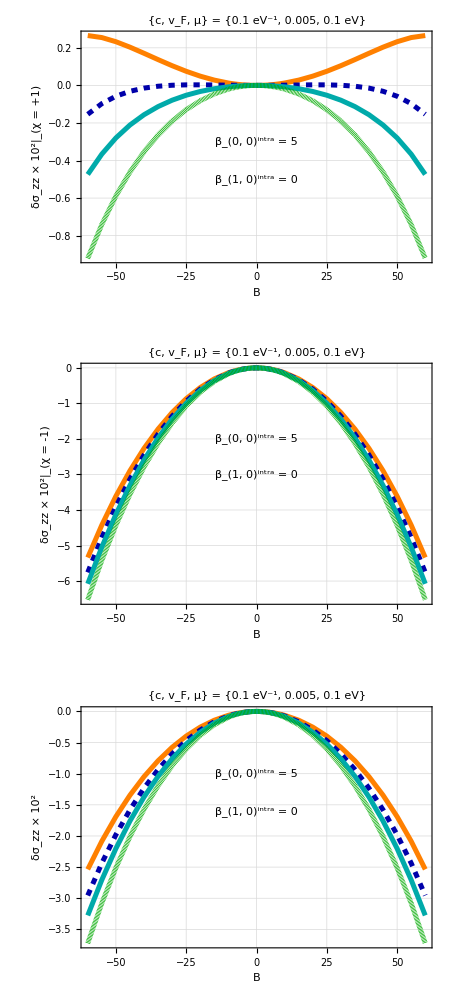

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat11,dat21,dat31,dat41},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = +1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 5",{0,-0.3}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-0.5}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];

g2=ListPlot[{dat12,dat22,dat32,dat42},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = -1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 5",{0,-2}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-3}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];


g3=ListPlot[{dat13,dat23,dat33,dat43},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 5",{0,-1.0}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-1.6}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];
leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{FontFamily->"Times",18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1},{g2},{g3}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig3a.pdf",Rasterize[pl],ImageResolution->100];
```

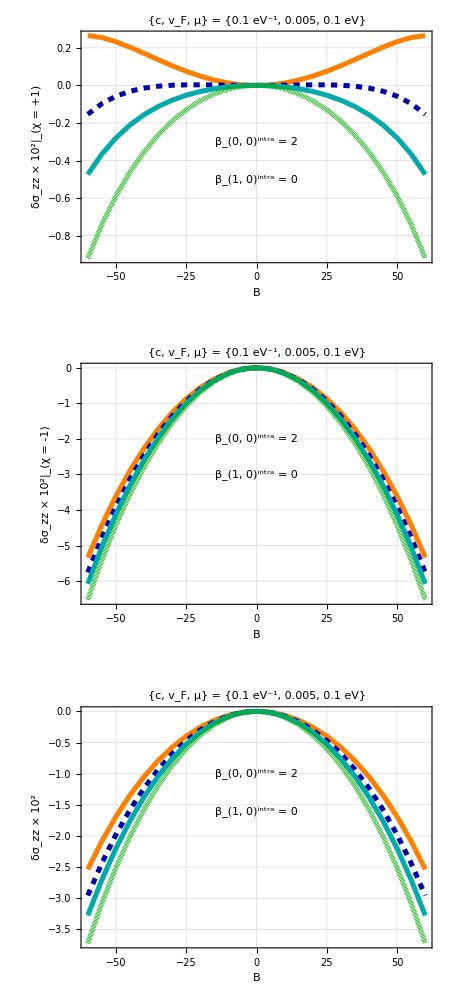

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat51,dat61,dat71,dat81},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = +1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 2",{0,-0.3}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-0.5}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];

g2=ListPlot[{dat52,dat62,dat72,dat82},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = -1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 2",{0,-2}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-3}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];

g3=ListPlot[{dat53,dat63,dat73,dat83},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 2",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-1.6}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];
leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{FontFamily->"Times",18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
 pl=Legended[GraphicsGrid[{{g1},{g2},{g3}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig3b.pdf",Rasterize[pl],ImageResolution->100];
```

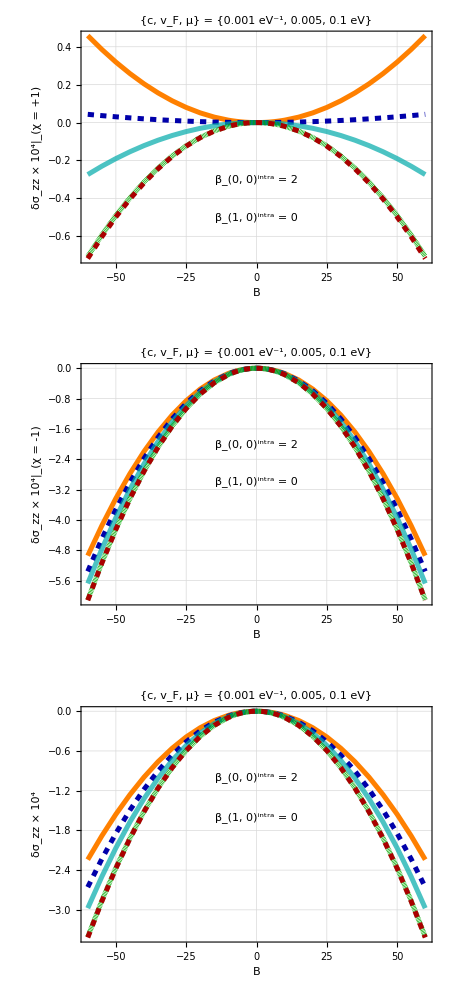

{0.5,1,2,50,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]],Directive[Darker[Red],Thickness[0.008],Dashing[0.01]]};

g1=ListPlot[{dat91,dat101,dat111,dat121,dat131},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^4|_(χ = +1)"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 2",{0,-0.3}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-0.5}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];

g2=ListPlot[{dat92,dat102,dat112,dat122,dat132},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^4|_(χ = -1)"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 2",{0,-2}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-3}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];

g3=ListPlot[{dat93,dat103,dat113,dat123,dat133},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^4"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(0, 0)^intra = 2",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{0,-1.6}],Darker[Brown],16,Bold]}(*******),PlotTheme->"Detailed",PlotLegends->None];

(* {0.5,0.02,0.001} *)
leg=LineLegend[style,{"0.5","1","2","50","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1},{g2},{g3}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4p,rat5p}
SetDirectory[NotebookDirectory[]];
Export["fig3c.pdf",Rasterize[pl],ImageResolution->100];
```

## fitting with powers of B

```mathematica
list1={{0.1,0.00002666666700773371},{1.1,0.00002666670793114246},{2.1,0.000026666817015279095},{3.1,0.000026666994137468125},{4.1,0.000026667239098125963},{5.1,0.000026667551620423053},{6.1,0.000026667931349814515},{7.1,0.000026668377853437767},{8.1,0.000026668890619375042},{9.1,0.000026669469055778534},{10.1,0.000026670112489855176},{15,0.00002667417702835846},{20,0.00002667978691496619},{25,0.0000266866910945567},{30,0.000026694639216892764},{35,0.00002670330216213203},{40,0.00002671225486813508},{45,0.00002672095231411117},{50,0.000026728695707592066},{55,0.00002673458417887193},{60,0.000026737444288334162}};
list2={{0.1,0.00002666666300777056},{1.1,0.000026666223930105285},{2.1,0.000026665052958070793},{3.1,0.00002666314982356799},{4.1,0.00002666051409057234},{5.1,0.000026657145154613575},{6.1,0.000026653042242053175},{7.1,0.000026648204409157592},{8.1,0.000026642630540964697},{9.1,0.00002663631934994006},{10.1,0.000026629269374419538},{15,0.000026583985110872897},{20,0.00002651917642013563},{25,0.000026435190461000524},{30,0.00002633150317093951},{35,0.000026207439451900967},{40,0.00002606214819126683},{45,0.000025894568037474347},{50,0.000025703380314879247},{55,0.000025486943447232907},{60,0.000025243199867154455}};
list3={{0.1,0.00005333333001550427},{1.1,0.00005333293186124775},{2.1,0.00005333186997334989},{3.1,0.00005333014396103612},{4.1,0.0000533277531886983},{5.1,0.00005332469677503663},{6.1,0.000053320973591867687},{7.1,0.00005331658226259536},{8.1,0.00005331152116033974},{9.1,0.00005330578840571859},{10.1,0.00005329938186427472},{15,0.00005325816213923136},{20,0.00005319896333510182},{25,0.000053121881555557226},{30,0.000053026142387832275},{35,0.000052910741614032995},{40,0.000052774403059401915},{45,0.00005261552035158552},{50,0.00005243207602247131},{55,0.000052221527626104835},{60,0.00005198064415548862}};

len=Length[list1];
x=0.00005333333333333329;
rat1=0.5;
scale=1/x;
dat11=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] *2scale-1)10^2},{i,1,len}]];
dat12=Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] *2scale-1)10^2},{i,1,len}]];
dat13=Join[{{0,0}},Table[{list3[[i,1]],(list3[[i,2]] *scale-1)10^2},{i,1,len}]];
Clear[ffit1,ffit2];
ffit1[B_]=b B^2+ c B^4/.FindFit[dat11,b B^2+ c B^4,{b,c},B]
ffit2[B_]=b B^2+ c B^4/.FindFit[dat12,b B^2+ c B^4,{b,c},B]
```

0.000132847 B^2-1.62527×10^-8 B^4

-0.00136483 B^2-3.25192×10^-8 B^4

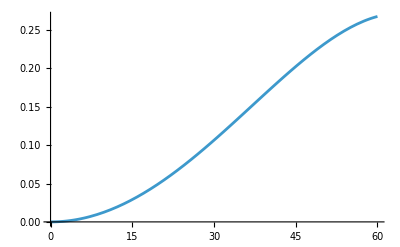

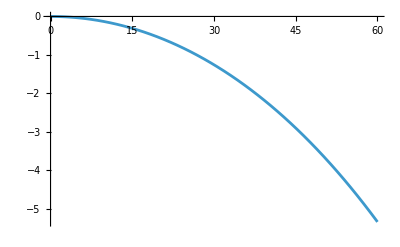

```mathematica
Plot[ffit1[B],{B,0,60}]
Plot[ffit2[B],{B,0,60}]
```